Our Old Code stuff

## Making data

### Control Case: Randomly choose rule IGNORE THIS

```mathematica
Clear["Global`*"]
SetSystemOptions["ParallelOptions"->"ParallelThreadNumber"->1];
(*Sets up nice computer memry partitions*)

(*setsup the rule table in a way the code can use*)
rulelabels=Table[IntegerDigits[i,2,8],{i,0,255}];
subrules=Reverse[Tuples[{0,1},3]];
ruletable=Table[Rule@@@Transpose[{subrules,rulelabels[[i]]}],{i,1,256}];

(*set up initial parameters*)
width=3;
timesteps=2^width;
ics=Tuples[{0,1},width];
(*CHANGE HERE*) rules={15,27,29,39,43,45,51,53,57,71,75,77,83,85,89,99,101,113,142,154,156,166,170,172,178,180,184,198,202,204,210,212,216,226,228,240};

(*Now it's going to do a loop within a loop. It loops over all reversible rules and then it loops over all possible initial conditions*)
data=
Table[
Table[

oic=ics[[i]];
orule=rules[[k]];
orule=rule;

(*****organism setup*****)
state=oic;
initialstate=state;

(******Check to change rule at every time step******)
(*Organism before the mutation*)
ruleone=rule;
stateone=state;

smallsteps=Table[
(*Take the current environment state and the current organism state and compare them in an arbitrary way*)
(*Take the output of that arbitrary comparison and determine one of the six rules from it: JK PICK A RANDOM RULE INSTEAD*)
(*Apply that new rule to the current organism state*)
(*rename the new organism state to stateone*)
(*rename the new rule of the organism to ruleone*)
(*Put these replacements in the rule, making a new rule.*)
(*CHANGE HERE*) newrule1=RandomChoice[{15,27,29,39,43,45,51,53,57,71,75,77,83,85,89,99,101,113,142,154,156,166,170,172,178,180,184,198,202,204,210,212,216,226,228,240}];
newrule=ruletable[[newrule1+1]];
(*Apply the rule to the state*)
step=Nest[Partition[#,3,1,2]/.newrule&,state,1];
state=step;
rule=newrule;
(*OUTPUT of the table! will be the organism state and the organism rule*)
{state,Flatten[Position[ruletable,rule]-1]}
,{j,1,timesteps}];
(*Has a weird output*)

CAorganism=First/@smallsteps;
organismrules=Last/@smallsteps//Flatten;
{CAorganism,organismrules}

,{k,1,Length[rules]}]
,{i,1,Length[ics]}];


(*Save the data to a file*)
Export["RandomRules_width"<>ToString[width]<>".csv",data]
```

RandomRules_width3.csv

### Env -> Org :::::::::: RERUN

```mathematica
(*Sets up nice computer memory partitions*)
Clear["Global`*"]
SetSystemOptions["ParallelOptions"->"ParallelThreadNumber"->1];
(*setsup the rule table in a way the code can use*)
rulelabels=Table[IntegerDigits[i,2,8],{i,0,255}];
subrules=Reverse[Tuples[{0,1},3]];
ruletable=Table[Rule@@@Transpose[{subrules,rulelabels[[i]]}],{i,1,256}];
(*set up initial parameters*)
width=3;
timesteps=2*2^width;
ics=Tuples[{0,1},width];


(*!!!!!!!!!CHANGE HERE!!!!!!!!!*) rules={15,27,29,39,43,45,51,53,57,71,75,77,83,85,89,99,101,113,142,154,156,166,170,172,178,180,184,198,202,204,210,212,216,226,228,240};


(*First, our initial conditions are something like <envinronment initial cond, environment rule, organism init cond, organism rule>. So we gotta set those up*)

(*Well for width 3, that gives is 80K possible initial conditions. XD So let's just randomly pick 1000 for now*)
worldics = RandomSample[Tuples[{ics,rules,ics,rules}],width*1000];


(*Okies, now we do a loops over all our world initial conditions!*)
data=
Table[

eic = worldics[[i]][[1]];
erule = worldics[[i]][[2]];
oic=worldics[[i]][[3]]; 
orule=worldics[[i]][[4]];

(*set up the organism*)
state=oic;
rule=orule;
(*set up the environment*)
environment = CellularAutomaton[erule,eic,timesteps];

smallsteps=
Table[
number=width*Total[state]+width*Total[environment[[j]]];
If[number>255,
newnumber=number-255,
newnumber = number];
newrule=Nearest[rules,newnumber][[1]];
newrule1=ruletable[[newrule+1]];
(*Apply that new rule to the current organism state*)
step=Nest[Partition[#,3,1,2]/.newrule1&,state,1];
(*rename the new organism state to 'state'*)
state=step;
(*rename the new rule of the organism to 'rule'*)
rule=newrule;

(*OUTPUT of the table! will be the organism state and the organism rule*)
{state,environment[[j]],Flatten[Position[ruletable,newrule1]-1]}

(*Do this for the specified number of timesteps*)
,{j,1,timesteps}];



(*Makes the table's output prettier*)
f[x_]:=x[[2]];
environment=f/@smallsteps;
CAorganism=First/@smallsteps;
organismrules=Last/@smallsteps//Flatten;
{environment,CAorganism,organismrules}

,{i,1,Length[worldics]}];

Export["Case2_Width"<>ToString[width]<>".csv",data]
```

Case2_Width3.csv

## Going through the data

### Initial Plots

```mathematica
width=3;
data=Import["Case2_Width"<>ToString[width]<>".csv"]//ToExpression;
ics=Tuples[{0,1},width];
possibletrajectories=Flatten[Table[Table[CellularAutomaton[i,ics[[j]],2*2^width-1],{i,0,255}],{j,1,Length[ics]}],1];
```

```mathematica
results=Table[
inno=If[
MemberQ[possibletrajectories,data[[i]][[2]]]==True,1,0];
info=
If[MemberQ[{ConstantArray[1,width],ConstantArray[0,width]},data[[i]][[2]][[1]]]==False,
1,0];
b={data[[i]][[2]],data[[i]][[3]]}//Transpose;
c=Table[Count[b[[1;;i]],b[[i]]],{i,1,Length[b]}];
d=Split[c];
If[Length[d]==1,
rt = "+";
att="NA";
oee1=1;
oee2="NA";
oee3=If[inno==1&&info==0,1,0];
oee4 = If[inno==0&&info==1,1,0];
,
rt = Length[d[[1]]];
att=Length/@d[[2;;Length[d]]]//Mean//Round;
oee1=If[inno==1&&info==1&&rt>2^width,1,0];
oee2=If[inno==1&&info==1&&rt>2^width&&att>2^width,1,0];
oee3=If[inno==1&&info==0&&rt>2^width,1,0];
oee4 = If[inno==0&&info==1&&rt>2^width,1,0];
];
{inno,info,rt,att,oee1,oee2,oee3,oee4}
,{i,1,Length[data]}];
```

RESULTS KEY: {innovative in states?, information-containing?, recurrence time, attractor size, is it oee?, is it oee in attractor too?, is it oee with no information?, oee without innovation?}
			1				2			3	       4		5		6				7				8
We are looking for OEE regardless of innovative states

```mathematica
OEEPercent =(((Last/@results)//Total)/Length[results]//N)100
```

26.7667

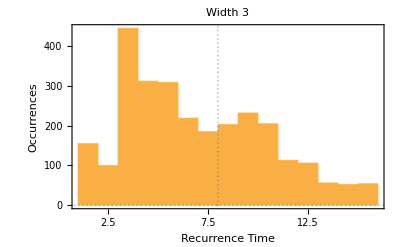

RT_Width3.pdf

```mathematica
f[x_]:=x[[3]]
plot=Histogram[DeleteCases[f/@results,"+"],PlotLabel->"Width "<>ToString[width],PlotTheme->"Business",FrameLabel->{"Recurrence Time","Occurences"},GridLines->{{2^width}, {0}}]
Export["RT_Width"<>ToString[width]<>".pdf",plot]
```

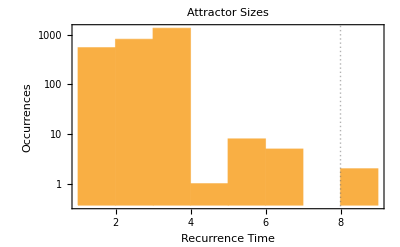

Att_Width3.pdf

```mathematica
f[x_]:=x[[4]]
Histogram[DeleteCases[f/@results,"NA"],PlotLabel->"Width "<>ToString[width],ScalingFunctions->"Log",PlotTheme->"Business",FrameLabel->{"Attractor Size","Occurrences"},GridLines->{{2^width}, {0}}]
Export["Att_Width"<>ToString[width]<>".pdf",plot]
```

### But what do they meaaaannnn

```mathematica
rr=
Table[
width=k;
timesteps=2^width;
ics=Tuples[{0,1},width];
rules=Range[0,255];

DeleteCases[Table[
If[
(Table[CellularAutomaton[rules[[i]],ics[[j]],1]//Last,{j,1,Length[ics]}]//Gather//Length)== 2^width,
rules[[i]]
]
,{i,1,Length[rules]}],Null]

,{k,3,9}]//Column
```

{15,27,29,39,43,45,51,53,57,71,75,77,83,85,89,99,101,113,142,154,156,166,170,172,178,180,184,198,202,204,210,212,216,226,228,240}
{15,51,85,105,150,170,204,240}
{15,45,51,75,85,89,101,105,150,154,166,170,180,204,210,240}
{15,51,85,170,204,240}
{15,45,51,75,85,89,101,105,150,154,166,170,180,204,210,240}
{15,51,85,105,150,170,204,240}
{15,45,51,75,85,89,101,154,166,170,180,204,210,240}

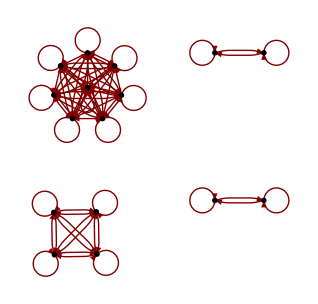

StateDiagram_Width4.pdf

```mathematica
width=4;
icsw=Tuples[{0,1},width];
steps=
Flatten[Table[Table[CellularAutomaton[rr[[width-2]][[j]],icsw[[i]],1],{i,1,Length[icsw]}],{j,1,Length[rr]}],1]//DeleteDuplicates;
f[x_]:=x[[1]]->x[[2]];
g=f/@steps;

diagram=GraphPlot[g,VertexRenderingFunction->(With[{p={Darker[Blue,.7],Point[#]}},Inset[ArrayPlot[{#2},Mesh->True,Frame->False,ImageSize->4{ Length[#2],1}],#]]&),DirectedEdges->True]

Export["StateDiagram_Width"<>ToString[width]<>".pdf",diagram]
```

## Old random code bits

### Make Histograms

```mathematica
Table[
width=m;
data = Import["RandomRules_width"<>ToString[width]<>".csv"]//ToExpression;
data2=Table[
Table[
a=data[[j]][[i]][[1]];
b=data[[j]][[i]][[2]];

If[MemberQ[a,ConstantArray[0,width]]||MemberQ[a,ConstantArray[1,width]],
whereitstops=DeleteCases[{Position[a,ConstantArray[0,width]][[1]],Position[a,ConstantArray[1,width]][[1]]},{}⟦1⟧]//Flatten//Min;
trajectory=a[[1;;whereitstops]];
ruletrajectory=b[[1;;whereitstops]],
trajectory=a;
ruletrajectory=b];

{trajectory//Length,ruletrajectory}
,{i,1,Length[data[[j]]]}],
{j,1,Length[data]}];
data3=
Flatten/@(Reverse/@Flatten[
Table[
Table[
Table[{data2[[k]][[j]][[1]],data2[[k]][[j]][[2]][[i]]},{i,1,Length[data2[[k]][[j]][[2]]]}]
,{j,1,Length[data2[[k]]]}]
,{k,1,Length[data2]}]
,2]//Tally);

(* LabelingFunction->(Placed[#[[1]],Above]&), *)
BubbleChart[data3,PlotLabel->"Width = "<>ToString[width],FrameLabel->{"Rule","Trajectory Length"},BubbleSizes->{0.01,0.1},LabelingFunction->(Placed[#[[1]],Tooltip]&),PlotTheme->"Business",AspectRatio->1/2,ImageSize->Medium]
,{m,3,7}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

These are plots that show how rules are related to trajectory length
Problem is, that trajectory length is totally decided by the initial conditions here: All information encoded in the IC is retained over time since these rules are reversable.
Most trajectories are going to be full length
Trajectories depend on ICs, not rules since information is preserved

### Older code bits!

```mathematica
Clear["Global`*"]
SetSystemOptions["ParallelOptions"->"ParallelThreadNumber"->1];
(*Sets up nice computer memry partitions*)
```

#### This is the stuff you can set to change the initial conditions

```mathematica
rulelabels=Table[IntegerDigits[i,2,8],{i,0,255}];
subrules=Reverse[Tuples[{0,1},3]];
ruletable=Table[Rule@@@Transpose[{subrules,rulelabels[[i]]}],{i,1,256}];

(*Set the initial conditions*)
width=3;
oic=RandomChoice[{0,1},width];
orule=RandomChoice[{15,51,85,170,204,240}];
ics={eic,oic,erule,orule}
```

{eic,{0,0,0},erule,51}

#### All this stuff is based on your initial conditions

```mathematica
(*Just ignore this*)
(*maxcompression=Table[
g[x_]:=IntegerDigits[x,2,w];
g/@RandomInteger[{0,2^w-1},2^width*2^w]//Compress//ByteCount
,{10000}]//Max;*)
```

```mathematica
(*defining more stuff, actually this is redundant*)
erule=ics[[3]];
orule=ics[[4]];
eIC=ics[[1]];
oIC=ics[[2]];
timesteps=200;
```

```mathematica
(*****environment setup*****)
environment=CellularAutomaton[erule,eIC,timesteps-1];
```

CellularAutomaton::nspecnl: Since rule specification erule is not a List, it must be an integer or a pure Boolean function.

```mathematica
(*****organism setup*****)
state=oIC;
initialstate=state;
```

```mathematica
(******Check to change rule at every time step******)
(*Organism before the mutation*)
ruleone=rule;
stateone=state;

smallsteps=Table[
(*Take the current environment state and the current organism state and compare them in an arbitrary way*)
(*Take the output of that arbitrary comparison and determine one of the six rules from it: JK PICK A RANDOM RULE INSTEAD*)
(*Apply that new rule to the current organism state*)
(*rename the new organism state to stateone*)
(*rename the new rule of the organism to ruleone*)
(*Put these replacements in the rule, making a new rule.*)
newrule1=RandomChoice[{15,51,85,170,204,240}];
newrule=ruletable[[newrule1+1]];
(*Apply the rule to the state*)
step=Nest[Partition[#,3,1,2]/.newrule&,state,1];
state=step;
rule=newrule;
(*OUTPUT of the table! will be the organism state and the organism rule*)
{state,Flatten[Position[ruletable,rule]-1]}
,{j,1,timesteps}];
(*Has a weird output*)
```

#### This is your output!

```mathematica
(******Raw Data*******)
CAorganism=First/@smallsteps;
organismrules=Last/@smallsteps;
Row[{Column[{"Environment",environment//ArrayPlot}],Column[{"Organism",CAorganism//ArrayPlot}]}]
```

ArrayPlot::mat: Argument CellularAutomaton[erule,eic,199] at position 1 is not a list of lists.

Environment
ArrayPlot[CellularAutomaton[erule,eic,199]]Organism
-Graphics-

```mathematica
(*(*Calculates the mutation rate*)
f[x_]:=x[[2]];
mutationrates=f/@smallsteps;
mutationpercent=(mutationrates/. 0->a /. _Integer->1 /. a ->0 //Total)/timesteps;*)
```

```mathematica
(*(*Compression*)
compression=(Compress[CAorganism]//ByteCount)/maxcompression//N;*)
```

```mathematica
(*(******Lyp Data*******)
timesteps=ics[[m]][[6]];
iniA=CAorganism[[1]];
iniB=ReplacePart[iniA,Ceiling[(width-1)/2]->Abs[iniA[[Ceiling[(width-1)/2]]]-1]];
Defects=ConstantArray[0,timesteps];
Defects[[1]]=Abs[iniA-iniB];

Do[
ruleDef=IntegerDigits[organismrules[[b]],2,8];
rule=MapThread[#->#2&,{Tuples[{1,0},3],ruleDef}];
StateAN=Partition[Prepend[Append[iniA,Last[iniA]],First[iniA]],3,1]/.rule;
Defects[[b+1]]=Total[Abs[(Abs[Map[ConstantArray[#,3]&,Partition[Prepend[Append[iniA,Last[iniA]],First[iniA]],3,1]]-ConstantArray[{{1,0,0},{0,1,0},{0,0,1}},width]]/.rule)-StateAN]*Partition[Append[Prepend[Defects[[b]],First@Defects[[b]]],Last@Defects[[b]]],3,1],{2}];
iniA=StateAN;
,{b,1,timesteps-1}];

lypdata=Transpose[{Range[1,timesteps],Map[Total,Defects]}];
model= Exp[k*t];
fit=FindFit[lypdata,model,k,t,WorkingPrecision->3];*)
```

### Which rules are reversable

```mathematica
(*set up initial parameters*)

Table[
width=k;
timesteps=2^width;
ics=Tuples[{0,1},width];
rules=Range[0,255];

DeleteCases[Table[
If[
(Table[CellularAutomaton[rules[[i]],ics[[j]],1]//Last,{j,1,Length[ics]}]//Gather//Length)== 2^width,
rules[[i]]
]
,{i,1,Length[rules]}],Null]

,{k,3,7}]//Column
```

{15,27,29,39,43,45,51,53,57,71,75,77,83,85,89,99,101,113,142,154,156,166,170,172,178,180,184,198,202,204,210,212,216,226,228,240}
{15,51,85,105,150,170,204,240}
{15,45,51,75,85,89,101,105,150,154,166,170,180,204,210,240}
{15,51,85,170,204,240}
{15,45,51,75,85,89,101,105,150,154,166,170,180,204,210,240}
{15,51,85,105,150,170,204,240}

:3
Ok so plotting the rules wasn’t helpful at all
Plot state transition maps for trajectories
For each rule, what are on a common trajectory? Which trajectories match these rules, just for the reversable rule
Gonna have loops and things, what’s that list, unique trajectories that that rule has
Then measure how weird the trajectories are, something non-trivial about the rule transitions
Cut off trajectotores until all 0’s or all 1’s
Are there any rules over-represented in long trajectories? How often the rules change, the output was still consitent was the same rule, how often does the landscape changes, distance measure between rules
How often is a rule used as a function of trajectory
Trajectory length vs % sampled
All traejcoties of certain length, how many rule transitions, how many transitions were of a particular rule, so many times we would have seen that rule
Then see the correlation to state landscapes

Then compare to old experiemnts and how often there reversable rules were present in OEE cases
Maximize number of trajectores to get to different states

Doug: Doesn’t want to explore statement, drive to fixed point attractors to model regenerations, a small set
State and history dependent, map between states and rules, trying to minimize pattern changes but couldn’t find solutions for that
feed-forward (decision tree) looks ‘smoother’ than recurrent, recurrent breaks the smoothness (has backwards edges in the neural net)

Sara: 3 and 3, one is CG version of eachother, rule 60
Randomized topology for rule 150 or a CA (assume white cells on edge)
State dependent topology

New things

## Make new data

### These rules are reversable

```mathematica
(*set up initial parameters*)

rr=Table[
width=k;
timesteps=2^width;
ics=Tuples[{0,1},width];
rules=Range[0,255];

DeleteCases[Table[
If[
Round[(Table[CellularAutomaton[rules[[i]],ics[[j]],1]//Last,{j,1,Length[ics]}]//Gather//Length)/ 2^width,0.1]==0,
rules[[i]]
]
,{i,1,Length[rules]}],Null]

,{k,3,7}]
```

{{},{},{0,255},{0,255},{0,255}}

### Env -> Org :::::::::: RERUN THIS!

Run for widths 3-7, lists of reversable rules needs to be changed for each width

```mathematica
(*Sets up nice computer memory partitions*)
Clear["Global`*"]
SetSystemOptions["ParallelOptions"->"ParallelThreadNumber"->1];
(*setsup the rule table in a way the code can use*)
rr=Table[
width=k;
timesteps=2^width;
ics=Tuples[{0,1},width];
rules=Range[0,255];

DeleteCases[Table[
If[
Round[(Table[CellularAutomaton[rules[[i]],ics[[j]],1]//Last,{j,1,Length[ics]}]//Gather//Length)/ 2^width,0.1]==0.5,
rules[[i]]
]
,{i,1,Length[rules]}],Null]

,{k,3,7}];

rulelabels=Table[IntegerDigits[i,2,8],{i,0,255}];
subrules=Reverse[Tuples[{0,1},3]];
ruletable=Table[Rule@@@Transpose[{subrules,rulelabels[[i]]}],{i,1,256}];
(*set up initial parameters*)
width=4;
timesteps=2*2^width;
ics=Tuples[{0,1},width];

rules=rr[[width-2]];
(*First, our initial conditions are something like <envinronment initial cond, environment rule, organism init cond, organism rule>. So we gotta set those up*)

(*Well for width 3, that gives is 80K possible initial conditions. XD So let's just randomly pick 1000 for now*)
worldics = RandomSample[Tuples[{ics,rules,ics,rules}],width*1000];

(*Okies, now we do a loops over all our world initial conditions!*)
data=
Table[

eic = worldics[[i]][[1]];
erule = worldics[[i]][[2]];
oic=worldics[[i]][[3]]; 
orule=worldics[[i]][[4]];

(*set up the organism*)
state=oic;
rule=orule;
(*set up the environment*)
environment = CellularAutomaton[erule,eic,timesteps];

smallsteps=
Table[
number=width*Total[state]+width*Total[environment[[j]]]+rule;
If[number>255,
newnumber=number-255,
newnumber = number];
newrule=Nearest[rules,newnumber][[1]];
newrule1=ruletable[[newrule+1]];
(*Apply that new rule to the current organism state*)
step=Nest[Partition[#,3,1,2]/.newrule1&,state,1];
(*rename the new organism state to 'state'*)
state=step;
(*rename the new rule of the organism to 'rule'*)
rule=newrule;

(*OUTPUT of the table! will be the organism state and the organism rule*)
{state,environment[[j]],Flatten[Position[ruletable,newrule1]-1]}

(*Do this for the specified number of timesteps*)
,{j,1,timesteps}];



(*Makes the table's output prettier*)
f[x_]:=x[[2]];
environment=f/@smallsteps;
CAorganism=First/@smallsteps;
organismrules=Last/@smallsteps//Flatten;
{erule,environment,CAorganism,organismrules}

,{i,1,Length[worldics]}];

Export["50_EnvOrg_Width"<>ToString[width]<>".csv",data]
```

50_EnvOrg_Width4.csv

## Process new data

```mathematica
Clear["Global`*"]
SetSystemOptions["ParallelOptions"->"ParallelThreadNumber"->1];
```

### Pre-process the data!

```mathematica
rr=Table[
width=k;
timesteps=2^width;
ics=Tuples[{0,1},width];
rules=Range[0,255];

DeleteCases[Table[
If[
Round[(Table[CellularAutomaton[rules[[i]],ics[[j]],1]//Last,{j,1,Length[ics]}]//Gather//Length)/ 2^width,0.1]==0.3,
rules[[i]]
]
,{i,1,Length[rules]}],Null]

,{k,3,7}]
```

{{},{2,8,16,64,191,239,247,253},{4,10,12,18,24,32,34,36,46,48,66,68,72,80,116,139,175,183,187,189,207,209,219,221,223,231,237,243,245,251},{1,4,12,18,32,34,46,48,68,72,116,127,128,139,183,187,207,209,221,223,237,243,251,254},{18,36,72,126,129,183,219,237}}

```mathematica
width=7;
data=Import["10_EnvOrg_Width"<>ToString[width]<>".csv"]//ToExpression;
ics=Tuples[{0,1},width];
possibletrajectories=Flatten[Table[Table[CellularAutomaton[i,ics[[j]],2*2^width-1],{i,0,255}],{j,1,Length[ics]}],1];
rr=Table[
widthca=k;
timesteps=2^widthca;
ics=Tuples[{0,1},widthca];
rules=Range[0,255];

DeleteCases[Table[
If[
Round[(Table[CellularAutomaton[rules[[i]],ics[[j]],1]//Last,{j,1,Length[ics]}]//Gather//Length)/ 2^widthca,0.1]==0.1,
rules[[i]]
]
,{i,1,Length[rules]}],Null]
,{k,3,7}];
rulelabels=Table[IntegerDigits[i,2,8],{i,0,255}];
subrules=Reverse[Tuples[{0,1},3]];
ruletable=Table[Rule@@@Transpose[{subrules,rulelabels[[i]]}],{i,1,256}];

rules=rr[[width-2]];
```

```mathematica
results=Table[
inno=If[
MemberQ[possibletrajectories,data[[i]][[3]]]==True,0,1];
info=
If[MemberQ[{ConstantArray[1,width],ConstantArray[0,width]},data[[i]][[2]][[1]]]==False,
1,0];
b={data[[i]][[3]],data[[i]][[4]]}//Transpose;
c=Table[Count[b[[1;;i]],b[[i]]],{i,1,Length[b]}];
d=Split[c];
If[Length[d]==1,
rt = "+";
att="NA";
oee1=1;
oee2="NA";
oee3=If[inno==1&&info==0,1,0];
oee4 = If[inno==0&&info==1,1,0];
,
rt = Length[d[[1]]];
att=Length/@d[[2;;Length[d]]]//Mean//Round;
oee1=If[inno==1&&info==1&&rt>2^width,1,0];
oee2=If[inno==1&&info==1&&rt>2^width&&att>2^width,1,0];
oee3=If[inno==1&&info==0&&rt>2^width,1,0];
oee4 = If[inno==0&&info==1&&rt>2^width,1,0];
];
{inno,info,rt,att,oee1,oee2,oee3,oee4}
,{i,1,Length[data]}];
```

RESULTS KEY: {innovative in states?, information-containing?, recurrence time, attractor size, is it oee?, is it oee in attractor too?, is it oee with no information?, oee without innovation?}
			1				2			3	       4		5		6				7				8

Wouldn’t it be cool to get those full recurrence times? :D

```mathematica
m=2;
```

```mathematica
betterresults=
Table[
If[results[[k]][[3]]=="+",

timesteps=m*2*2^width;

eic = data[[k]][[2]][[1]];
erule = data[[k]][[1]];
oic=data[[k]][[3]][[1]]; 
orule=data[[k]][[4]][[1]];

(*set up the organism*)
state=oic;
rule=orule;
(*set up the environment*)
environment = CellularAutomaton[erule,eic,timesteps];

smallsteps=
Table[
number=width*Total[state]+width*Total[environment[[j]]]+rule;
If[number>255,
newnumber=number-255,
newnumber = number];
newrule=Nearest[rules,newnumber][[1]];
newrule1=ruletable[[newrule+1]];
(*Apply that new rule to the current organism state*)
step=Nest[Partition[#,3,1,2]/.newrule1&,state,1];
(*rename the new organism state to 'state'*)
state=step;
(*rename the new rule of the organism to 'rule'*)
rule=newrule;

(*OUTPUT of the table! will be the organism state and the organism rule*)
{state,environment[[j]],Flatten[Position[ruletable,newrule1]-1]}

(*Do this for the specified number of timesteps*)
,{j,1,timesteps}];

(*Makes the table's output prettier*)
f[x_]:=x[[2]];
environment=f/@smallsteps;
CAorganism=First/@smallsteps;
organismrules=Last/@smallsteps//Flatten;
data1={erule,environment,CAorganism,organismrules};

inno=1;
info=
If[MemberQ[{ConstantArray[1,width],ConstantArray[0,width]},data1[[3]][[1]]]==False,
1,0];
b={data1[[3]],data1[[4]]}//Transpose;
c=Table[Count[b[[1;;i]],b[[i]]],{i,1,Length[b]}];
d=Split[c];
If[Length[d]>2,
rt = Length[d[[1]]];
att=Length/@d[[2;;Length[d]]]//Mean//Round;
oee1=If[inno==1&&info==1&&rt>2^width,1,0];
oee2=If[inno==1&&info==1&&rt>2^width&&att>2^width,1,0];
oee3=If[inno==1&&info==0&&rt>2^width,1,0];
oee4 = If[inno==0&&info==1&&rt>2^width,1,0];
{inno,info,rt,att,oee1,oee2,oee3,oee4},
{"+","+","+","+","+","+","+","+"}]
,
results[[k]]
]
,{k,1,Length[results]}];

If[(betterresults//Flatten//Tally//Sort//Reverse//First//First)=="+",
n=m+1;
m=n;
results=betterresults;
Print["Keep going.... "<>ToString[m]],
Export["10_EnvOrg_Width"<>ToString[width]<>"_Results.csv",betterresults];
Print["STOP"]
]
```

STOP

If this cell outputs “Keep going...” that just means to run it again. Keep rerunning that cell until it says “STOP”.

### Redo the plots we had before...

RESULTS KEY: {innovative in states?, information-containing?, recurrence time, attractor size, is it oee?, is it oee in attractor too?, is it oee with no information?, oee without innovation?}
			1				2			3	       4		5		6				7				8

```mathematica
Table[
width=w;

If[FileExistsQ["00_EnvOrg_Width"<>ToString[width]<>"_Results.csv"]==True,
betterresults=Import["00_EnvOrg_Width"<>ToString[width]<>"_Results.csv"]//ToExpression;
f[x_]:=x[[5]];
OEEPercent =(((f/@betterresults)//Total)/Length[betterresults]//N)100;

f[x_]:=x[[3]];
a=f/@betterresults//Tally;
b=Last/@a//Total;
c=Transpose[{First/@a,(Last/@a)/b}]//Sort;
d=ListLogPlot[c,Filling->Axis,PlotLabel->"R = 0.0, w = "<>ToString[width],PlotTheme->"Business",FrameLabel->{"t_r","% of O (log)"},GridLines->{{{2^width,{Thick,Red}}}, Automatic},
ImageSize->Medium];
Export["00_EnvOrg_Width"<>ToString[width]<>"_RT.pdf",d];

g[x_]:=x[[4]];
a=g/@betterresults//Tally;
b=Last/@a//Total;
c=Transpose[{First/@a,(Last/@a)/b}]//Sort;
d=ListLogPlot[c,Filling->Axis,PlotLabel->"R = 0.0, w = "<>ToString[width],PlotTheme->"Business",FrameLabel->{"t_a","% of O (log)"},GridLines->{{{2^width,{Thick,Red}}}, Automatic},
ImageSize->Medium];
Export["00_EnvOrg_Width"<>ToString[width]<>"_AT.pdf",d];]
,{w,3,7}]
```

{Null,Null,Null,Null,Null}

```mathematica
Table[
Table[
percent=y;
p=percent/100//N;
width=w;

If[FileExistsQ[ToString[percent]<>"_EnvOrg_Width"<>ToString[width]<>"_Results.csv"]==True,
betterresults=Import[ToString[percent]<>"_EnvOrg_Width"<>ToString[width]<>"_Results.csv"]//ToExpression;
f[x_]:=x[[5]];
OEEPercent =(((f/@betterresults)//Total)/Length[betterresults]//N)100;

f[x_]:=x[[3]];
a=f/@betterresults//Tally;
b=Last/@a//Total;
c=Transpose[{First/@a,(Last/@a)/b}]//Sort;
d=ListLogPlot[c,Filling->Axis,PlotLabel->"R = "<>ToString[p]<>", w = "<>ToString[width],PlotTheme->"Business",FrameLabel->{"t_r","% of O (log)"},GridLines->{{{2^width,{Thick,Red}}}, Automatic},
ImageSize->Medium];
Export[ToString[percent]<>"_EnvOrg_Width"<>ToString[width]<>"_RT.pdf",d];

g[x_]:=x[[4]];
a=g/@betterresults//Tally;
b=Last/@a//Total;
c=Transpose[{First/@a,(Last/@a)/b}]//Sort;
d=ListLogPlot[c,Filling->Axis,PlotLabel->"R = "<>ToString[p]<>", w = "<>ToString[width],PlotTheme->"Business",FrameLabel->{"t_a","% of O (log)"},GridLines->{{{2^width,{Thick,Red}}}, Automatic},
ImageSize->Medium];
Export[ToString[percent]<>"_EnvOrg_Width"<>ToString[width]<>"_AT.pdf",d];
]
,{w,3,7}]
,{y,90,0,-10}]
```

{{Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null}}

```mathematica
FileExistsQ[ToString[percent]<>"_EnvOrg_Width"<>ToString[width]<>"_Results.csv"]
```

False

### State transition diagrams

```mathematica
Table[

p=percent/100//N;

rr=Table[
widthca=k;
timesteps=2^widthca;
ics=Tuples[{0,1},widthca];
rules=Range[0,255];

DeleteCases[Table[
If[
Round[(Table[CellularAutomaton[rules[[i]],ics[[j]],1]//Last,{j,1,Length[ics]}]//Gather//Length)/ 2^widthca,0.1]==p,
rules[[i]]
]
,{i,1,Length[rules]}],Null]
,{k,3,7}];

Table[
width=n;
icsw=Tuples[{0,1},width];

If[Length[rr[[width-2]]]>0,
steps=
Flatten[Table[Table[CellularAutomaton[rr[[width-2]][[j]],icsw[[i]],1],{i,1,Length[icsw]}],{j,1,Length[rr[[width-2]]]}],1]//DeleteDuplicates;
f[x_]:=x[[1]]->x[[2]];
g=f/@steps;

diagram=Graph[g,(*VertexRenderingFunction->(With[{p={Darker[Blue,.7],Point[#]}},Inset[ArrayPlot[{#2},Mesh->True,Frame->False,ImageSize->4{ Length[#2],1}],#]]&),*)DirectedEdges->True,ImageSize->Small];

Export[ToString[percent]<>"StateDiagram_Width"<>ToString[width]<>".pdf",diagram]
]
,{n,3,7}]

,{percent,100,-1,-10}]
```

{{100StateDiagram_Width3.pdf,100StateDiagram_Width4.pdf,100StateDiagram_Width5.pdf,100StateDiagram_Width6.pdf,100StateDiagram_Width7.pdf},{90StateDiagram_Width3.pdf,90StateDiagram_Width4.pdf,Null,90StateDiagram_Width6.pdf,Null},{Null,80StateDiagram_Width4.pdf,80StateDiagram_Width5.pdf,80StateDiagram_Width6.pdf,80StateDiagram_Width7.pdf},{Null,70StateDiagram_Width4.pdf,70StateDiagram_Width5.pdf,70StateDiagram_Width6.pdf,70StateDiagram_Width7.pdf},{60StateDiagram_Width3.pdf,60StateDiagram_Width4.pdf,Null,60StateDiagram_Width6.pdf,60StateDiagram_Width7.pdf},{50StateDiagram_Width3.pdf,50StateDiagram_Width4.pdf,50StateDiagram_Width5.pdf,50StateDiagram_Width6.pdf,50StateDiagram_Width7.pdf},{Null,40StateDiagram_Width4.pdf,40StateDiagram_Width5.pdf,40StateDiagram_Width6.pdf,40StateDiagram_Width7.pdf},{Null,30StateDiagram_Width4.pdf,30StateDiagram_Width5.pdf,30StateDiagram_Width6.pdf,30StateDiagram_Width7.pdf},{20StateDiagram_Width3.pdf,20StateDiagram_Width4.pdf,20StateDiagram_Width5.pdf,20StateDiagram_Width6.pdf,20StateDiagram_Width7.pdf},{10StateDiagram_Width3.pdf,10StateDiagram_Width4.pdf,Null,Null,10StateDiagram_Width7.pdf},{Null,Null,0StateDiagram_Width5.pdf,0StateDiagram_Width6.pdf,0StateDiagram_Width7.pdf}}

### Histogram of In/Out degree averages of trajectories, OEE in states and rules (not just rules)

```mathematica
Table[
width=o;

If[FileExistsQ["00_EnvOrg_Width"<>ToString[width]<>"_Results.csv"]==True,
data=Import["00_EnvOrg_Width"<>ToString[width]<>".csv"]//ToExpression;
data1=Import["00_EnvOrg_Width"<>ToString[width]<>"_Results.csv"]//ToExpression;

percent=0;
p=percent/100//N;

rr=Table[
widthca=k;
timesteps=2^widthca;
ics=Tuples[{0,1},widthca];
rules=Range[0,255];

DeleteCases[Table[
If[
Round[(Table[CellularAutomaton[rules[[i]],ics[[j]],1]//Last,{j,1,Length[ics]}]//Gather//Length)/ 2^widthca,0.1]==p,
rules[[i]]
]
,{i,1,Length[rules]}],Null]
,{k,3,7}];

icsw=Tuples[{0,1},width];

If[Length[rr[[width-2]]]>0,
steps=
Flatten[Table[Table[CellularAutomaton[rr[[width-2]][[j]],icsw[[i]],1],{i,1,Length[icsw]}],{j,1,Length[rr[[width-2]]]}],1]//DeleteDuplicates;
f[x_]:=x[[1]]->x[[2]];
g=f/@steps];
graph=Graph[g];


trajectories=Table[

a=Table[
VertexInDegree[graph,data[[j]][[3]][[i]]]
,{i,1,Length[data[[2]][[3]]]}];
b=Table[
VertexOutDegree[graph,data[[j]][[3]][[i]]]
,{i,1,Length[data[[j]][[3]]]}];
io=(a/b)//Mean;
oee=data1[[j]][[5]];
{io,oee}

,{j,1,Length[data]}];

{First/@(GatherBy[trajectories,Last][[1]])//Mean,Last/@(GatherBy[trajectories,Last][[1]])//Mean,If[Length[GatherBy[trajectories,Last]]>1,First/@(GatherBy[trajectories,Last][[2]])//Mean],Length[GatherBy[trajectories,Last][[1]]],If[Length[GatherBy[trajectories,Last]]>1,Length[GatherBy[trajectories,Last][[2]]]]}
]
,{o,3,7}]
```

{Null,Null,{16,0,Null,500,Null},{32,0,Null,6000,Null},{64,0,Null,7000,Null}}

Avg in/out for non-OEE, 0 means first is for non-OEE, avg in/out for OEE, number of non-OEE, number of OEE

```mathematica
Table[Table[
width=o;
percent=q;
p=percent/100//N;

If[FileExistsQ[ToString[percent]<>"_EnvOrg_Width"<>ToString[width]<>"_Results.csv"]==True,
data=Import[ToString[percent]<>"_EnvOrg_Width"<>ToString[width]<>".csv"]//ToExpression;
data1=Import[ToString[percent]<>"_EnvOrg_Width"<>ToString[width]<>"_Results.csv"]//ToExpression;

rr=Table[
widthca=k;
timesteps=2^widthca;
ics=Tuples[{0,1},widthca];
rules=Range[0,255];

DeleteCases[Table[
If[
Round[(Table[CellularAutomaton[rules[[i]],ics[[j]],1]//Last,{j,1,Length[ics]}]//Gather//Length)/ 2^widthca,0.1]==p,
rules[[i]]
]
,{i,1,Length[rules]}],Null]
,{k,3,7}];

icsw=Tuples[{0,1},width];

If[Length[rr[[width-2]]]>0,
steps=
Flatten[Table[Table[CellularAutomaton[rr[[width-2]][[j]],icsw[[i]],1],{i,1,Length[icsw]}],{j,1,Length[rr[[width-2]]]}],1]//DeleteDuplicates;
f[x_]:=x[[1]]->x[[2]];
g=f/@steps];
graph=Graph[g];


trajectories=Table[

a=Table[
VertexInDegree[graph,data[[j]][[3]][[i]]]
,{i,1,Length[data[[2]][[3]]]}];
b=Table[
VertexOutDegree[graph,data[[j]][[3]][[i]]]
,{i,1,Length[data[[j]][[3]]]}];
io=(a/b)//Mean;
oee=data1[[j]][[5]];
{io,oee}

,{j,1,Length[data]}];

{First/@(GatherBy[trajectories,Last][[1]])//Mean,Last/@(GatherBy[trajectories,Last][[1]])//Mean,If[Length[GatherBy[trajectories,Last]]>1,First/@(GatherBy[trajectories,Last][[2]])//Mean],Length[GatherBy[trajectories,Last][[1]]],If[Length[GatherBy[trajectories,Last]]>1,Length[GatherBy[trajectories,Last][[2]]]]}

]
,{o,3,7}]
,{q,100,0,-10}]
```

{{Null,Null,Null,Null,Null},{{1,0,1,2435,565},{999/800,0,Null,4000,Null},Null,{2749679/2304000,0,Null,6000,Null},Null},{Null,{1694315/310784,1,213331/37728,2428,1572},{2840947/603136,0,2387/2304,4712,288},{1852397/512000,0,Null,6000,Null},{12736039/10223616,0,652769/528384,6656,344}},{Null,{12918739/2502528,1,2962193/540736,2793,1207},{25297823/4321280,1,28074773/2826240,1688,3312},{155242531/15360000,0,Null,6000,Null},{239178787/215040000,0,Null,7000,Null}},{{42599/12720,1,266263/70560,795,2205},{83901/18536,1,683509/125664,2317,1683},Null,{23195262095/6368986624,0,361454783/295896832,5117,883},{699223619719/28309811200,0,278785309/215797760,6743,257}},{{166871/65472,1,2129/659,1023,1977},{2180037/293248,0,797745/109376,2291,1709},{8837449/588800,0,1049161/81920,4600,400},{257474241/11776000,0,Null,6000,Null},{151324833053/6872279040,0,273618581/224040960,6779,221}},{Null,{465115/71936,0,1955/256,3934,66},{4442813/480000,0,Null,5000,Null},{12142777/512000,0,Null,6000,Null},{515986443361/13069056000,0,Null,7000,Null}},{Null,{872231/192000,0,Null,4000,Null},{2110192633/177526272,0,2090923/2449216,4503,497},{7211377301/253440000,0,Null,6000,Null},{345424207/7168000,0,Null,7000,Null}},{{4,0,Null,3000,Null},{1685297/256000,0,Null,4000,Null},{358201/38400,0,Null,5000,Null},{54071867/3840000,0,Null,6000,Null},{801331073/24640000,0,Null,7000,Null}},{{4,0,Null,30,Null},{8,0,Null,400,Null},Null,Null,{17812037/672000,0,Null,7000,Null}},{Null,Null,Null,Null,Null}}

```mathematica
heat={{{1,0,1,2274,726},{1,0,Null,4000,Null},{218345/215552,0,6063129/5942272,1684,3316},{1,0,Null,6000,Null},{87687323/87463936,0,12941811/12888064,6101,899}},{{1,0,1,2435,565},{999/800,0,Null,4000,Null},Null,{2749679/2304000,0,Null,6000,Null},Null},{Null,{1694315/310784,1,213331/37728,2428,1572},{2840947/603136,0,2387/2304,4712,288},{1852397/512000,0,Null,6000,Null},{12736039/10223616,0,652769/528384,6656,344}},{Null,{12918739/2502528,1,2962193/540736,2793,1207},{25297823/4321280,1,28074773/2826240,1688,3312},{155242531/15360000,0,Null,6000,Null},{239178787/215040000,0,Null,7000,Null}},{{42599/12720,1,266263/70560,795,2205},{83901/18536,1,683509/125664,2317,1683},Null,{23195262095/6368986624,0,361454783/295896832,5117,883},{699223619719/28309811200,0,278785309/215797760,6743,257}},{{166871/65472,1,2129/659,1023,1977},{2180037/293248,0,797745/109376,2291,1709},{8837449/588800,0,1049161/81920,4600,400},{257474241/11776000,0,Null,6000,Null},{151324833053/6872279040,0,273618581/224040960,6779,221}},{Null,{465115/71936,0,1955/256,3934,66},{4442813/480000,0,Null,5000,Null},{12142777/512000,0,Null,6000,Null},{515986443361/13069056000,0,Null,7000,Null}},{Null,{872231/192000,0,Null,4000,Null},{2110192633/177526272,0,2090923/2449216,4503,497},{7211377301/253440000,0,Null,6000,Null},{345424207/7168000,0,Null,7000,Null}},{{4,0,Null,3000,Null},{1685297/256000,0,Null,4000,Null},{358201/38400,0,Null,5000,Null},{54071867/3840000,0,Null,6000,Null},{801331073/24640000,0,Null,7000,Null}},{{4,0,Null,30,Null},{8,0,Null,400,Null},Null,Null,{17812037/672000,0,Null,7000,Null}},{Null,Null,{16,0,Null,500,Null},{32,0,Null,6000,Null},{64,0,Null,7000,Null}}}/.Null->"a";
```

```mathematica
nonoeeheat=
Table[
Table[

If[(heat[[j]][[i]]//Length)==5,
If[heat[[j]][[i]][[2]]==0,
heat[[j]][[i]][[1]],
heat[[j]][[i]][[3]]]
,"a"]

,{i,1,Length[heat[[j]]]}]
,{j,1,Length[heat]}]//N;
```

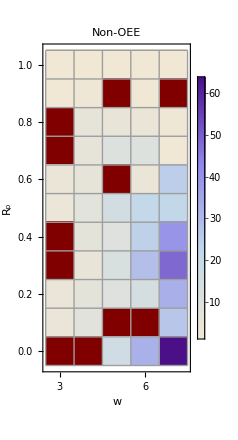

```mathematica
no=ArrayPlot[nonoeeheat,PlotLegends->Automatic,PlotLabel->Style["Non-OEE",14] ,FrameTicks->{{{{1,"1.0"},{3,"0.8"},{5,"0.6"},{7,"0.4"},{9,"0.2"},{11,"0.0"}},None},{{{1,"3"},{2,"4"},{3,"5"},{4,"6"},{5,"7"}},None}},ColorFunction->ColorData[{"LakeColors","Reverse"}],FrameLabel->{"R_p","w"},Mesh->True,Frame->True]
```

```mathematica
Export["nonoee_traj.pdf",no]
```

nonoee_traj.pdf

```mathematica
oeeheat=
Table[
Table[

If[(heat[[j]][[i]]//Length)==5,
If[heat[[j]][[i]][[2]]==0,
heat[[j]][[i]][[3]],
heat[[j]][[i]][[1]]]
,"a"]

,{i,1,Length[heat[[j]]]}]
,{j,1,Length[heat]}]//N;
```

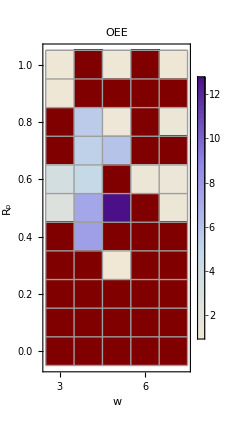

```mathematica
o=ArrayPlot[oeeheat,PlotLegends->Automatic,PlotLabel->Style["OEE",14] ,FrameTicks->{{{{1,"1.0"},{3,"0.8"},{5,"0.6"},{7,"0.4"},{9,"0.2"},{11,"0.0"}},None},{{{1,"3"},{2,"4"},{3,"5"},{4,"6"},{5,"7"}},None}},ColorFunction->ColorData[{"LakeColors","Reverse"}],FrameLabel->{"R_p","w"},Mesh->True,Frame->True]
```

```mathematica
Export["oee_trajectories.pdf",o]
```

oee_trajectories.pdf

```mathematica
oee=
Table[
Table[

If[(heat[[j]][[i]]//Length)==5,
If[heat[[j]][[i]][[5]]=="a",
0,
heat[[j]][[i]][[5]]/(heat[[j]][[i]][[4]]+heat[[j]][[i]][[5]])
]
,"a"]

,{i,1,Length[heat[[j]]]}]
,{j,1,Length[heat]}]//N
```

{{0.242,0.,0.6632,0.,0.128429},{0.188333,0.,a,0.,a},{a,0.393,0.0576,0.,0.0491429},{a,0.30175,0.6624,0.,0.},{0.735,0.42075,a,0.147167,0.0367143},{0.659,0.42725,0.08,0.,0.0315714},{a,0.0165,0.,0.,0.},{a,0.,0.0994,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,a,a,0.},{a,a,0.,0.,0.}}

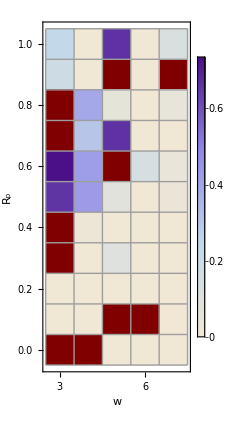

```mathematica
oeeheat=ArrayPlot[oee,PlotLegends->Automatic, FrameTicks->{{{{1,"1.0"},{3,"0.8"},{5,"0.6"},{7,"0.4"},{9,"0.2"},{11,"0.0"}},None},{{{1,"3"},{2,"4"},{3,"5"},{4,"6"},{5,"7"}},None}},ColorFunction->ColorData[{"LakeColors","Reverse"}],FrameLabel->{"R_p","w"},Mesh->True,Frame->True]
```

```mathematica
Export["oee.pdf",oeeheat]
```

oee.pdf

### Super Big Heatmap

```mathematica
heat={{{1,0,1,2274,726},{1,0,Null,4000,Null},{218345/215552,0,6063129/5942272,1684,3316},{1,0,Null,6000,Null},{87687323/87463936,0,12941811/12888064,6101,899}},{{1,0,1,2435,565},{999/800,0,Null,4000,Null},Null,{2749679/2304000,0,Null,6000,Null},Null},{Null,{1694315/310784,1,213331/37728,2428,1572},{2840947/603136,0,2387/2304,4712,288},{1852397/512000,0,Null,6000,Null},{12736039/10223616,0,652769/528384,6656,344}},{Null,{12918739/2502528,1,2962193/540736,2793,1207},{25297823/4321280,1,28074773/2826240,1688,3312},{155242531/15360000,0,Null,6000,Null},{239178787/215040000,0,Null,7000,Null}},{{42599/12720,1,266263/70560,795,2205},{83901/18536,1,683509/125664,2317,1683},Null,{23195262095/6368986624,0,361454783/295896832,5117,883},{699223619719/28309811200,0,278785309/215797760,6743,257}},{{166871/65472,1,2129/659,1023,1977},{2180037/293248,0,797745/109376,2291,1709},{8837449/588800,0,1049161/81920,4600,400},{257474241/11776000,0,Null,6000,Null},{151324833053/6872279040,0,273618581/224040960,6779,221}},{Null,{465115/71936,0,1955/256,3934,66},{4442813/480000,0,Null,5000,Null},{12142777/512000,0,Null,6000,Null},{515986443361/13069056000,0,Null,7000,Null}},{Null,{872231/192000,0,Null,4000,Null},{2110192633/177526272,0,2090923/2449216,4503,497},{7211377301/253440000,0,Null,6000,Null},{345424207/7168000,0,Null,7000,Null}},{{4,0,Null,3000,Null},{1685297/256000,0,Null,4000,Null},{358201/38400,0,Null,5000,Null},{54071867/3840000,0,Null,6000,Null},{801331073/24640000,0,Null,7000,Null}},{{4,0,Null,30,Null},{8,0,Null,400,Null},Null,Null,{17812037/672000,0,Null,7000,Null}},{Null,Null,{16,0,Null,500,Null},{32,0,Null,6000,Null},{64,0,Null,7000,Null}}}/.Null->"a";
```

```mathematica
oee=
Table[
Table[

If[(heat[[j]][[i]]//Length)==5,
If[heat[[j]][[i]][[5]]=="a",
0,
heat[[j]][[i]][[5]]/(heat[[j]][[i]][[4]]+heat[[j]][[i]][[5]])
]
,"a"]

,{i,1,Length[heat[[j]]]}]
,{j,1,Length[heat]}]//N;
```

```mathematica
oeebig=ArrayPlot[oee,PlotLegends->Automatic ,FrameTicks->{{{{1,"1.0"},{3,"0.8"},{5,"0.6"},{7,"0.4"},{9,"0.2"},{11,"0.0"}},None},{{{1,"3"},{2,"4"},{3,"5"},{4,"6"},{5,"7"}},None}},FrameLabel->{"R_p","w"},Mesh->True,Frame->True,ImageSize->Large]
```

-Graphics-

```mathematica
Export["oeebig.pdf", oeebig]
```

oeebig.pdf

```mathematica
states=GraphicsGrid[Table[

p=percent/100//N;

rr=Table[
widthca=k;
timesteps=2^widthca;
ics=Tuples[{0,1},widthca];
rules=Range[0,255];

DeleteCases[Table[
If[
Round[(Table[CellularAutomaton[rules[[i]],ics[[j]],1]//Last,{j,1,Length[ics]}]//Gather//Length)/ 2^widthca,0.1]==p,
rules[[i]]
]
,{i,1,Length[rules]}],Null]
,{k,3,7}];

Table[
width=n;
icsw=Tuples[{0,1},width];

If[Length[rr[[width-2]]]>0,
steps=
Flatten[Table[Table[CellularAutomaton[rr[[width-2]][[j]],icsw[[i]],1],{i,1,Length[icsw]}],{j,1,Length[rr[[width-2]]]}],1]//DeleteDuplicates;
f[x_]:=x[[1]]->x[[2]];
g=f/@steps;

diagram=Graph[g,(*VertexRenderingFunction->(With[{p={Darker[Blue,.7],Point[#]}},Inset[ArrayPlot[{#2},Mesh->True,Frame->False,ImageSize->4{ Length[#2],1}],#]]&),*)DirectedEdges->True,ImageSize->Small]

]
,{n,3,7}]

,{percent,100,-1,-10}],ImageSize->Large]
```

-Graphics-

```mathematica
Export["states.pdf",states]
```

states.pdf

### What environments give us the longest recurrence times?

### In N Out Degree Distributions for State Transition Diagrams

These plot suck, they don't really tell us anything!

```mathematica
Clear["Global`*"]
SetSystemOptions["ParallelOptions"->"ParallelThreadNumber"->1];
```

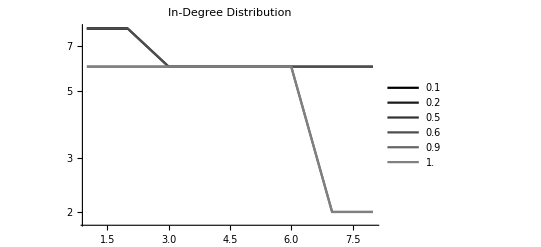
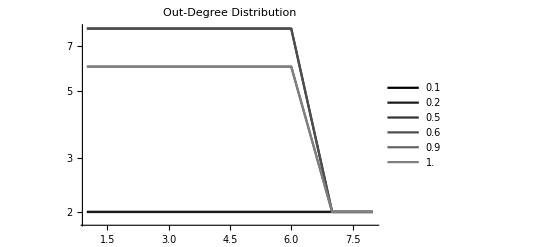
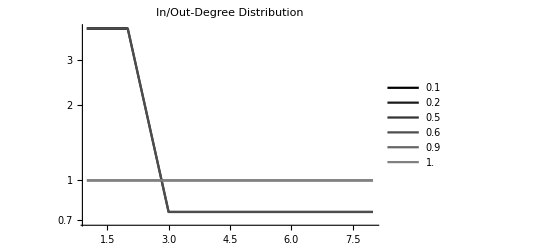
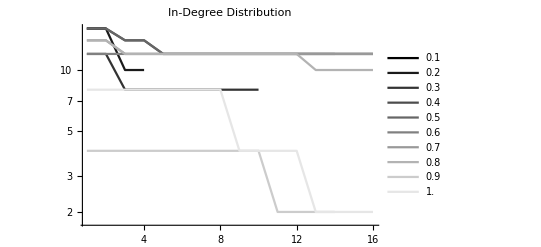
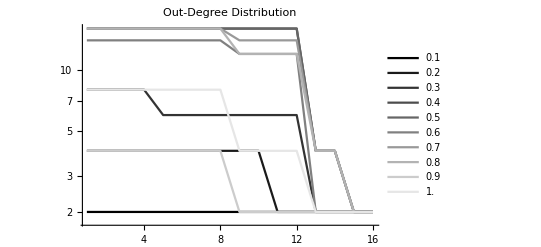
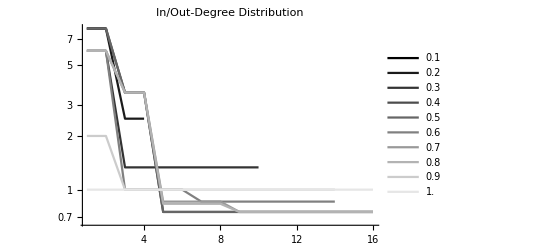
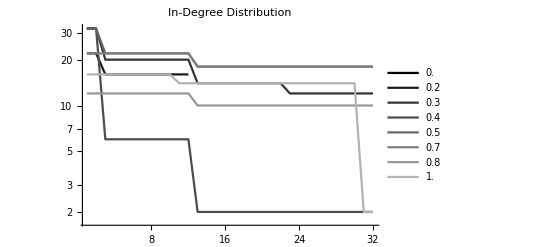
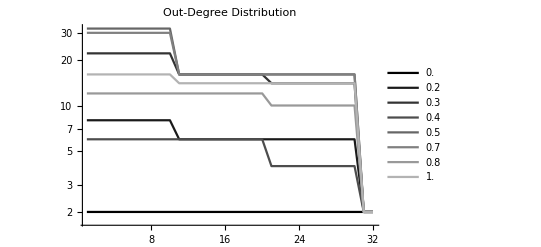
{WIDTH = 3,-Graphics-,-Graphics-,-Graphics-}
{WIDTH = 4,-Graphics-,-Graphics-,-Graphics-}
{WIDTH = 5,-Graphics-,-Graphics-,-Graphics-}
{WIDTH = 6,-Graphics-,-Graphics-,-Graphics-}
{WIDTH = 7,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[

lines=
DeleteCases[Table[

width=k;
timesteps=2^width;
ics=Tuples[{0,1},width];
rules=Range[0,255];

rr=DeleteCases[Table[
If[
Round[(Table[CellularAutomaton[rules[[i]],ics[[j]],1]//Last,{j,1,Length[ics]}]//Gather//Length)/ 2^width,0.1]==p,
rules[[i]]
]
,{i,1,Length[rules]}],Null];

If[rr≠{},
icsw=Tuples[{0,1},width];
steps=
Flatten[Table[Table[CellularAutomaton[rr[[j]],icsw[[i]],1],{i,1,Length[icsw]}],{j,1,Length[rr]}],1]//DeleteDuplicates;
f[x_]:=x[[1]]->x[[2]];
g=f/@steps;
{VertexInDegree[Graph[g]]//Sort//Reverse,VertexOutDegree[Graph[g]]//Sort//Reverse,(VertexInDegree[Graph[g]]/VertexOutDegree[Graph[g]])//Sort//Reverse,p}
]

,{p,0.0,1,0.1}]
,Null];


f[x_]:=x[[2]];
h[x_]:=x[[3]];
in=ListLogPlot[First/@lines,PlotRange->All,Joined->True,PlotLegends->Last/@lines,PlotStyle->Table[GrayLevel[i],{i,0,1,0.1}],PlotLabel->"In-Degree Distribution"];
out=ListLogPlot[f/@lines,PlotRange->All,Joined->True,PlotLegends->Last/@lines,PlotStyle->Table[GrayLevel[i],{i,0,1,0.1}],PlotLabel->"Out-Degree Distribution"];
inout=ListLogPlot[h/@lines,PlotRange->All,Joined->True,PlotLegends->Last/@lines,PlotStyle->Table[GrayLevel[i],{i,0,1,0.1}],PlotLabel->"In/Out-Degree Distribution"];
{"WIDTH = "<>ToString[k],in,out,inout}

,{k,3,7}]//Column
```

```mathematica
lines=Table[
p=1.0;
width=k;
timesteps=2^width;
ics=Tuples[{0,1},width];
rules=Range[0,255];

rr=DeleteCases[Table[
If[
Round[(Table[CellularAutomaton[rules[[i]],ics[[j]],1]//Last,{j,1,Length[ics]}]//Gather//Length)/ 2^width,0.1]==p,
rules[[i]]
]
,{i,1,Length[rules]}],Null];

If[rr≠{},
icsw=Tuples[{0,1},width];
steps=
Flatten[Table[Table[CellularAutomaton[rr[[j]],icsw[[i]],1],{i,1,Length[icsw]}],{j,1,Length[rr]}],1]//DeleteDuplicates;
f[x_]:=x[[1]]->x[[2]];
g=f/@steps;
{VertexInDegree[Graph[g]]//Sort//Reverse,VertexOutDegree[Graph[g]]//Sort//Reverse,(VertexInDegree[Graph[g]]/VertexOutDegree[Graph[g]])//Sort//Reverse}
]
,{k,3,7}]
```

{{{6,6,6,6,6,6,2,2},{6,6,6,6,6,6,2,2},{1,1,1,1,1,1,1,1}},{{8,8,8,8,8,8,8,8,4,4,4,4,2,2,2,2},{8,8,8,8,8,8,8,8,4,4,4,4,2,2,2,2},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}},{{16,16,16,16,16,16,16,16,16,16,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,2,2},{16,16,16,16,16,16,16,16,16,16,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,2,2},{8/7,8/7,8/7,8/7,8/7,8/7,8/7,8/7,8/7,8/7,1,1,1,1,1,1,1,1,1,1,1,1,7/8,7/8,7/8,7/8,7/8,7/8,7/8,7/8,7/8,7/8}},{{6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,2,2,2,2},{6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,2,2,2,2},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}},{{16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,2,2},{16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,2,2},{8/7,8/7,8/7,8/7,8/7,8/7,8/7,8/7,8/7,8/7,8/7,8/7,8/7,8/7,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,7/8,7/8,7/8,7/8,7/8,7/8,7/8,7/8,7/8,7/8,7/8,7/8,7/8,7/8}}}

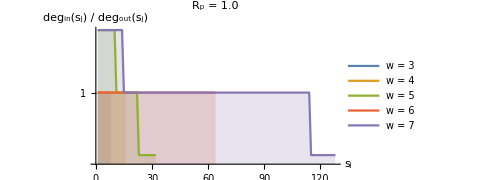

```mathematica
in=ListPlot[First/@lines,Joined->True,AxesLabel->{"v","deg_in(v)"},PlotLabel->"In-Degree Distribution, R = 0.5",ImageSize->Medium];
inout=ListLogPlot[Last/@lines,Filling->Axis,Joined->True,AxesLabel->{Style["s_j",12],Style["deg_in(s_j) / deg_out(s_j)",12]},PlotLabel->Style["R_p = 1.0",14],PlotLegends->{"w = 3","w = 4","w = 5","w = 6","w = 7"},PlotRange->{Automatic,Automatic},ImageSize->Medium, AspectRatio->1/2,TicksStyle->Directive["Label", 10]]
f[x_]:=x[[2]]
out = ListLogLogPlot[f/@lines,Joined->True,AxesLabel->{"v","deg_out(v)"},PlotLabel->"Out-Degree Distribution, R = 1.0",ImageSize->Medium];
```

```mathematica
Export["inoutp100.pdf",inout]
```

inoutp100.pdf

### Distribution of Reversable Rules per Width

Looks good!

```mathematica
rrs=
Table[
Table[

widthca=k;
timesteps=2^widthca;
ics=Tuples[{0,1},widthca];
rules=Range[0,255];

DeleteCases[Table[
If[
Round[(Table[CellularAutomaton[rules[[i]],ics[[j]],1]//Last,{j,1,Length[ics]}]//Gather//Length)/ 2^widthca,0.1]==p,
rules[[i]]
]
,{i,1,Length[rules]}],Null]//Length

,{k,3,7}]
,{p,0,1,0.1}]
```

{{0,0,2,2,2},{2,2,0,0,8},{14,6,8,20,28},{0,8,30,24,8},{0,40,8,8,40},{60,36,66,72,26},{108,48,0,72,100},{0,56,106,36,20},{0,48,20,8,8},{36,4,0,8,0},{36,8,16,6,16}}

```mathematica
pie=PieChart[rrs//Transpose,ChartLegends->Placed[Table[NumberForm[N[p],{3,1}],{p,0.0,1.0,0.1}],Right],ChartLabels->{Placed[Range[3,7],"RadialCenter"],None}, SectorSpacing->0,ChartStyle->"Rainbow"]
```

-Graphics-

```mathematica
Export["pie.pdf",pie]
```

pie.pdf

### Fusing rule networks together

Uh. How does this change the in/out degree distribution? How does that relate to longest recurrence times? Can we do this analytically?
>>> We need to think of how in/out degree affects the recurrence times. Also what does this mean thermodynmaically? --> Wolperts shit.
>>> Need to invent a measure of “entropy” or something along those lines. Could be a ratio of in/out degree over a trajectory. What about self loops?
Louiville’s Theorem? Does that relate to any of this at all?

## Reversible and Non-reversible interaction functions

### Current setup, w=5, p=1

```mathematica
width=5;
timesteps=2^width;
ics=Tuples[{0,1},width];
rules=Range[0,255];

rr=DeleteCases[Table[
If[
Round[(Table[CellularAutomaton[rules[[i]],ics[[j]],1]//Last,{j,1,Length[ics]}]//Gather//Length)/ 2^width,0.1]==1.0,
rules[[i]]
]
,{i,1,Length[rules]}],Null];

outs=Length[rr]
ins=outs+2*(width+1)
```

16

28

```mathematica
rulelabels=Table[IntegerDigits[i,2,8],{i,0,255}];
subrules=Reverse[Tuples[{0,1},3]];
ruletable=Table[Rule@@@Transpose[{subrules,rulelabels[[i]]}],{i,1,256}];
(*set up initial parameters*)
timesteps=2*2^width;
ics=Tuples[{0,1},width];

rules=rr;
(*First, our initial conditions are something like <envinronment initial cond, environment rule, organism init cond, organism rule>. So we gotta set those up*)

(*Well for width 3, that gives is 80K possible initial conditions. XD So let's just randomly pick 1000 for now*)
worldics = RandomSample[Tuples[{ics,rules,ics,rules}],width*1000];

(*Okies, now we do a loops over all our world initial conditions!*)
data=
Table[

eic = worldics[[i]][[1]];
erule = worldics[[i]][[2]];
oic=worldics[[i]][[3]]; 
orule=worldics[[i]][[4]];

(*set up the organism*)
state=oic;
rule=orule;
(*set up the environment*)
environment = CellularAutomaton[erule,eic,timesteps];

smallsteps=
Table[
number=width*Total[state]+width*Total[environment[[j]]]+rule;
If[number>255,
newnumber=number-255,
newnumber = number];
newrule=Nearest[rules,newnumber][[1]];
newrule1=ruletable[[newrule+1]];
(*Apply that new rule to the current organism state*)
step=Nest[Partition[#,3,1,2]/.newrule1&,state,1];
(*rename the new organism state to 'state'*)
state=step;
(*rename the new rule of the organism to 'rule'*)
rule=newrule;

(*OUTPUT of the table! will be the organism state and the organism rule*)
{state,environment[[j]],Flatten[Position[ruletable,newrule1]-1]}

(*Do this for the specified number of timesteps*)
,{j,1,timesteps}];



(*Makes the table's output prettier*)
f[x_]:=x[[2]];
environment=f/@smallsteps;
CAorganism=First/@smallsteps;
organismrules=Last/@smallsteps//Flatten;
{erule,environment,CAorganism,organismrules}

,{i,1,Length[worldics]}];
```

```mathematica
ics=Tuples[{0,1},width];
possibletrajectories=Flatten[Table[Table[CellularAutomaton[i,ics[[j]],2*2^width-1],{i,0,255}],{j,1,Length[ics]}],1];

results=Table[
inno=If[
MemberQ[possibletrajectories,data[[i]][[3]]]==True,0,1];
info=
If[MemberQ[{ConstantArray[1,width],ConstantArray[0,width]},data[[i]][[2]][[1]]]==False,
1,0];
b={data[[i]][[3]],data[[i]][[4]]}//Transpose;
c=Table[Count[b[[1;;i]],b[[i]]],{i,1,Length[b]}];
d=Split[c];
If[Length[d]==1,
rt = "+";
att="NA";
oee1=1;
oee2="NA";
oee3=If[inno==1&&info==0,1,0];
oee4 = If[inno==0&&info==1,1,0];
,
rt = Length[d[[1]]];
att=Length/@d[[2;;Length[d]]]//Mean//Round;
oee1=If[inno==1&&info==1&&rt>2^width,1,0];
oee2=If[inno==1&&info==1&&rt>2^width&&att>2^width,1,0];
oee3=If[inno==1&&info==0&&rt>2^width,1,0];
oee4 = If[inno==0&&info==1&&rt>2^width,1,0];
];
{inno,info,rt,att,oee1,oee2,oee3,oee4}
,{i,1,Length[data]}];
```

```mathematica
m=2;
```

```mathematica
betterresults=
Table[
If[results[[k]][[3]]=="+",

timesteps=m*2*2^width;

eic = data[[k]][[2]][[1]];
erule = data[[k]][[1]];
oic=data[[k]][[3]][[1]]; 
orule=data[[k]][[4]][[1]];

(*set up the organism*)
state=oic;
rule=orule;
(*set up the environment*)
environment = CellularAutomaton[erule,eic,timesteps];

smallsteps=
Table[
number=width*Total[state]+width*Total[environment[[j]]]+rule;
If[number>255,
newnumber=number-255,
newnumber = number];
newrule=Nearest[rules,newnumber][[1]];
newrule1=ruletable[[newrule+1]];
(*Apply that new rule to the current organism state*)
step=Nest[Partition[#,3,1,2]/.newrule1&,state,1];
(*rename the new organism state to 'state'*)
state=step;
(*rename the new rule of the organism to 'rule'*)
rule=newrule;

(*OUTPUT of the table! will be the organism state and the organism rule*)
{state,environment[[j]],Flatten[Position[ruletable,newrule1]-1]}

(*Do this for the specified number of timesteps*)
,{j,1,timesteps}];

(*Makes the table's output prettier*)
f[x_]:=x[[2]];
environment=f/@smallsteps;
CAorganism=First/@smallsteps;
organismrules=Last/@smallsteps//Flatten;
data1={erule,environment,CAorganism,organismrules};

inno=1;
info=
If[MemberQ[{ConstantArray[1,width],ConstantArray[0,width]},data1[[3]][[1]]]==False,
1,0];
b={data1[[3]],data1[[4]]}//Transpose;
c=Table[Count[b[[1;;i]],b[[i]]],{i,1,Length[b]}];
d=Split[c];
If[Length[d]>2,
rt = Length[d[[1]]];
att=Length/@d[[2;;Length[d]]]//Mean//Round;
oee1=If[inno==1&&info==1&&rt>2^width,1,0];
oee2=If[inno==1&&info==1&&rt>2^width&&att>2^width,1,0];
oee3=If[inno==1&&info==0&&rt>2^width,1,0];
oee4 = If[inno==0&&info==1&&rt>2^width,1,0];
{inno,info,rt,att,oee1,oee2,oee3,oee4},
{"+","+","+","+","+","+","+","+"}]
,
results[[k]]
]
,{k,1,Length[results]}];

If[(betterresults//Flatten//Tally//Sort//Reverse//First//First)=="+",
n=m+1;
m=n;
results=betterresults;
Print["Keep going.... "<>ToString[m]],
Print["STOP"]
]
```

STOP

RESULTS KEY: {innovative in states?, information-containing?, recurrence time, attractor size, is it oee?, is it oee in attractor too?, is it oee with no information?, oee without innovation?}
			1				2			3	       4		5		6				7				8

#### Percent oee and trajectory in/out

```mathematica
f[x_]:=x[[5]]
oeepercent=Total[f/@betterresults]/Length[f/@betterresults]
```

82/125

```mathematica
ics=Tuples[{0,1},width];
steps=
Flatten[Table[Table[CellularAutomaton[rr[[j]],ics[[i]],1],{i,1,Length[ics]}],{j,1,Length[rr]}],1]//DeleteDuplicates;
f[x_]:=x[[1]]->x[[2]];
g=f/@steps;

diagram=Graph[g,(*VertexRenderingFunction->(With[{p={Darker[Blue,.7],Point[#]}},Inset[ArrayPlot[{#2},Mesh->True,Frame->False,ImageSize->4{ Length[#2],1}],#]]&),*)DirectedEdges->True,ImageSize->Small];

trajectories=Table[

a=Table[
VertexInDegree[diagram,data[[j]][[3]][[i]]]
,{i,1,Length[data[[j]][[3]]]}];
b=Table[
VertexOutDegree[diagram,data[[j]][[3]][[i]]]
,{i,1,Length[data[[j]][[3]]]}];
io=(a/b)//Mean;
oee=betterresults[[j]][[5]];
{io,oee}

,{j,1,Length[data]}];

oeetraj=First/@(GroupBy[trajectories,Last]//Last)//Mean
nonoeetraj=First/@(GroupBy[trajectories,Last]//First)//Mean
```

3118429/3082240

11987461/11755520

### Max Ins, w=5, p=1

```mathematica
width=5;
timesteps=2^width;
ics=Tuples[{0,1},width];
rules=Range[0,255];

rr=DeleteCases[Table[
If[
Round[(Table[CellularAutomaton[rules[[i]],ics[[j]],1]//Last,{j,1,Length[ics]}]//Gather//Length)/ 2^width,0.1]==1.0,
rules[[i]]
]
,{i,1,Length[rules]}],Null];

outs=Length[rr]
ins=outs+2*(2^width)
```

16

80

```mathematica
rulelabels=Table[IntegerDigits[i,2,8],{i,0,255}];
subrules=Reverse[Tuples[{0,1},3]];
ruletable=Table[Rule@@@Transpose[{subrules,rulelabels[[i]]}],{i,1,256}];
(*set up initial parameters*)
timesteps=2*2^width;
ics=Tuples[{0,1},width];

rules=rr;
(*First, our initial conditions are something like <envinronment initial cond, environment rule, organism init cond, organism rule>. So we gotta set those up*)

(*Well for width 3, that gives is 80K possible initial conditions. XD So let's just randomly pick 1000 for now*)
worldics = RandomSample[Tuples[{ics,rules,ics,rules}],width*1000];

(*Okies, now we do a loops over all our world initial conditions!*)
data=
Table[

eic = worldics[[i]][[1]];
erule = worldics[[i]][[2]];
oic=worldics[[i]][[3]]; 
orule=worldics[[i]][[4]];

(*set up the organism*)
state=oic;
rule=orule;
(*set up the environment*)
environment = CellularAutomaton[erule,eic,timesteps];

smallsteps=
Table[
number=width*FromDigits[state,2]+width*FromDigits[environment[[j]],2]+rule;
If[number>255,
newnumber=number-255,
newnumber = number];
newrule=Nearest[rules,newnumber][[1]];
newrule1=ruletable[[newrule+1]];
(*Apply that new rule to the current organism state*)
step=Nest[Partition[#,3,1,2]/.newrule1&,state,1];
(*rename the new organism state to 'state'*)
state=step;
(*rename the new rule of the organism to 'rule'*)
rule=newrule;

(*OUTPUT of the table! will be the organism state and the organism rule*)
{state,environment[[j]],Flatten[Position[ruletable,newrule1]-1]}

(*Do this for the specified number of timesteps*)
,{j,1,timesteps}];



(*Makes the table's output prettier*)
f[x_]:=x[[2]];
environment=f/@smallsteps;
CAorganism=First/@smallsteps;
organismrules=Last/@smallsteps//Flatten;
{erule,environment,CAorganism,organismrules}

,{i,1,Length[worldics]}];
```

```mathematica
ics=Tuples[{0,1},width];
possibletrajectories=Flatten[Table[Table[CellularAutomaton[i,ics[[j]],2*2^width-1],{i,0,255}],{j,1,Length[ics]}],1];

results=Table[
inno=If[
MemberQ[possibletrajectories,data[[i]][[3]]]==True,0,1];
info=
If[MemberQ[{ConstantArray[1,width],ConstantArray[0,width]},data[[i]][[2]][[1]]]==False,
1,0];
b={data[[i]][[3]],data[[i]][[4]]}//Transpose;
c=Table[Count[b[[1;;i]],b[[i]]],{i,1,Length[b]}];
d=Split[c];
If[Length[d]==1,
rt = "+";
att="NA";
oee1=1;
oee2="NA";
oee3=If[inno==1&&info==0,1,0];
oee4 = If[inno==0&&info==1,1,0];
,
rt = Length[d[[1]]];
att=Length/@d[[2;;Length[d]]]//Mean//Round;
oee1=If[inno==1&&info==1&&rt>2^width,1,0];
oee2=If[inno==1&&info==1&&rt>2^width&&att>2^width,1,0];
oee3=If[inno==1&&info==0&&rt>2^width,1,0];
oee4 = If[inno==0&&info==1&&rt>2^width,1,0];
];
{inno,info,rt,att,oee1,oee2,oee3,oee4}
,{i,1,Length[data]}];
```

```mathematica
m=2;
```

```mathematica
betterresults=
Table[
If[results[[k]][[3]]=="+",

timesteps=m*2*2^width;

eic = data[[k]][[2]][[1]];
erule = data[[k]][[1]];
oic=data[[k]][[3]][[1]]; 
orule=data[[k]][[4]][[1]];

(*set up the organism*)
state=oic;
rule=orule;
(*set up the environment*)
environment = CellularAutomaton[erule,eic,timesteps];

smallsteps=
Table[
number=width*FromDigits[state,2]+width*FromDigits[environment[[j]],2]+rule;
If[number>255,
newnumber=number-255,
newnumber = number];
newrule=Nearest[rules,newnumber][[1]];
newrule1=ruletable[[newrule+1]];
(*Apply that new rule to the current organism state*)
step=Nest[Partition[#,3,1,2]/.newrule1&,state,1];
(*rename the new organism state to 'state'*)
state=step;
(*rename the new rule of the organism to 'rule'*)
rule=newrule;

(*OUTPUT of the table! will be the organism state and the organism rule*)
{state,environment[[j]],Flatten[Position[ruletable,newrule1]-1]}

(*Do this for the specified number of timesteps*)
,{j,1,timesteps}];

(*Makes the table's output prettier*)
f[x_]:=x[[2]];
environment=f/@smallsteps;
CAorganism=First/@smallsteps;
organismrules=Last/@smallsteps//Flatten;
data1={erule,environment,CAorganism,organismrules};

inno=1;
info=
If[MemberQ[{ConstantArray[1,width],ConstantArray[0,width]},data1[[3]][[1]]]==False,
1,0];
b={data1[[3]],data1[[4]]}//Transpose;
c=Table[Count[b[[1;;i]],b[[i]]],{i,1,Length[b]}];
d=Split[c];
If[Length[d]>2,
rt = Length[d[[1]]];
att=Length/@d[[2;;Length[d]]]//Mean//Round;
oee1=If[inno==1&&info==1&&rt>2^width,1,0];
oee2=If[inno==1&&info==1&&rt>2^width&&att>2^width,1,0];
oee3=If[inno==1&&info==0&&rt>2^width,1,0];
oee4 = If[inno==0&&info==1&&rt>2^width,1,0];
{inno,info,rt,att,oee1,oee2,oee3,oee4},
{"+","+","+","+","+","+","+","+"}]
,
results[[k]]
]
,{k,1,Length[results]}];

If[(betterresults//Flatten//Tally//Sort//Reverse//First//First)=="+",
n=m+1;
m=n;
results=betterresults;
Print["Keep going.... "<>ToString[m]],
Print["STOP"]
]
```

STOP

RESULTS KEY: {innovative in states?, information-containing?, recurrence time, attractor size, is it oee?, is it oee in attractor too?, is it oee with no information?, oee without innovation?}
			1				2			3	       4		5		6				7				8

#### Percent oee and trajectory in/out

```mathematica
f[x_]:=x[[5]]
oeepercent=Total[f/@betterresults]/Length[f/@betterresults]
```

661/2500

```mathematica
ics=Tuples[{0,1},width];
steps=
Flatten[Table[Table[CellularAutomaton[rr[[j]],ics[[i]],1],{i,1,Length[ics]}],{j,1,Length[rr]}],1]//DeleteDuplicates;
f[x_]:=x[[1]]->x[[2]];
g=f/@steps;

diagram=Graph[g,(*VertexRenderingFunction->(With[{p={Darker[Blue,.7],Point[#]}},Inset[ArrayPlot[{#2},Mesh->True,Frame->False,ImageSize->4{ Length[#2],1}],#]]&),*)DirectedEdges->True,ImageSize->Small];

trajectories=Table[

a=Table[
VertexInDegree[diagram,data[[j]][[3]][[i]]]
,{i,1,Length[data[[j]][[3]]]}];
b=Table[
VertexOutDegree[diagram,data[[j]][[3]][[i]]]
,{i,1,Length[data[[j]][[3]]]}];
io=(a/b)//Mean;
oee=betterresults[[j]][[5]];
{io,oee}

,{j,1,Length[data]}];

oeetraj=First/@(GroupBy[trajectories,Last]//Last)//Mean
nonoeetraj=First/@(GroupBy[trajectories,Last]//First)//Mean
```

4761633/4738048

1103831/1098496

### Ins = Outs, w=5, p=1 EASIEST

Outs is 16 for this case, can easily do 2*6=12 state-ins leaving 4 rule-ins left --> EASIEST
Can also do 8 rule-ins, leaving 8 state-ins, 4 for each state. 2^5=32, do 2:1 mapping 5 times

```mathematica
width=5;
timesteps=2^width;
ics=Tuples[{0,1},width];
rules=Range[0,255];

rr=DeleteCases[Table[
If[
Round[(Table[CellularAutomaton[rules[[i]],ics[[j]],1]//Last,{j,1,Length[ics]}]//Gather//Length)/ 2^width,0.1]==1.0,
rules[[i]]
]
,{i,1,Length[rules]}],Null];

outs=Length[rr]
ins=outs/4+2*(width+1)
```

16

16

```mathematica
rulelabels=Table[IntegerDigits[i,2,8],{i,0,255}];
subrules=Reverse[Tuples[{0,1},3]];
ruletable=Table[Rule@@@Transpose[{subrules,rulelabels[[i]]}],{i,1,256}];
(*set up initial parameters*)
timesteps=2*2^width;
ics=Tuples[{0,1},width];

rules=rr;
(*This is a convolution where four rules map to a single rule. This is a 4:1 mapping in the rule space*)
conv=Partition[rr,4];
(*First, our initial conditions are something like <envinronment initial cond, environment rule, organism init cond, organism rule>. So we gotta set those up*)

(*Well for width 3, that gives is 80K possible initial conditions. XD So let's just randomly pick 1000 for now*)
worldics = RandomSample[Tuples[{ics,rules,ics,rules}],width*1000];

(*Okies, now we do a loops over all our world initial conditions!*)
data=
Table[

eic = worldics[[i]][[1]];
erule = worldics[[i]][[2]];
oic=worldics[[i]][[3]]; 
orule=worldics[[i]][[4]];

(*set up the organism*)
state=oic;
rule=orule;
(*set up the environment*)
environment = CellularAutomaton[erule,eic,timesteps];

smallsteps=
Table[
number=width*Total[state]+width*Total[environment[[j]]]+conv[[Position[conv,rule][[1]]//First]][[1]];
If[number>255,
newnumber=number-255,
newnumber = number];
newrule=Nearest[rules,newnumber][[1]];
newrule1=ruletable[[newrule+1]];
(*Apply that new rule to the current organism state*)
step=Nest[Partition[#,3,1,2]/.newrule1&,state,1];
(*rename the new organism state to 'state'*)
state=step;
(*rename the new rule of the organism to 'rule'*)
rule=newrule;

(*OUTPUT of the table! will be the organism state and the organism rule*)
{state,environment[[j]],Flatten[Position[ruletable,newrule1]-1]}

(*Do this for the specified number of timesteps*)
,{j,1,timesteps}];



(*Makes the table's output prettier*)
f[x_]:=x[[2]];
environment=f/@smallsteps;
CAorganism=First/@smallsteps;
organismrules=Last/@smallsteps//Flatten;
{erule,environment,CAorganism,organismrules}

,{i,1,Length[worldics]}];
```

```mathematica
ics=Tuples[{0,1},width];
possibletrajectories=Flatten[Table[Table[CellularAutomaton[i,ics[[j]],2*2^width-1],{i,0,255}],{j,1,Length[ics]}],1];

results=Table[
inno=If[
MemberQ[possibletrajectories,data[[i]][[3]]]==True,0,1];
info=
If[MemberQ[{ConstantArray[1,width],ConstantArray[0,width]},data[[i]][[2]][[1]]]==False,
1,0];
b={data[[i]][[3]],data[[i]][[4]]}//Transpose;
c=Table[Count[b[[1;;i]],b[[i]]],{i,1,Length[b]}];
d=Split[c];
If[Length[d]==1,
rt = "+";
att="NA";
oee1=1;
oee2="NA";
oee3=If[inno==1&&info==0,1,0];
oee4 = If[inno==0&&info==1,1,0];
,
rt = Length[d[[1]]];
att=Length/@d[[2;;Length[d]]]//Mean//Round;
oee1=If[inno==1&&info==1&&rt>2^width,1,0];
oee2=If[inno==1&&info==1&&rt>2^width&&att>2^width,1,0];
oee3=If[inno==1&&info==0&&rt>2^width,1,0];
oee4 = If[inno==0&&info==1&&rt>2^width,1,0];
];
{inno,info,rt,att,oee1,oee2,oee3,oee4}
,{i,1,Length[data]}];
```

```mathematica
m=2;
```

```mathematica
betterresults=
Table[
If[results[[k]][[3]]=="+",

timesteps=m*2*2^width;

eic = data[[k]][[2]][[1]];
erule = data[[k]][[1]];
oic=data[[k]][[3]][[1]]; 
orule=data[[k]][[4]][[1]];

(*set up the organism*)
state=oic;
rule=orule;
(*set up the environment*)
environment = CellularAutomaton[erule,eic,timesteps];

smallsteps=
Table[
number=width*Total[state]+width*Total[environment[[j]]]+conv[[Position[conv,rule][[1]]//First]][[1]];
If[number>255,
newnumber=number-255,
newnumber = number];
newrule=Nearest[rules,newnumber][[1]];
newrule1=ruletable[[newrule+1]];
(*Apply that new rule to the current organism state*)
step=Nest[Partition[#,3,1,2]/.newrule1&,state,1];
(*rename the new organism state to 'state'*)
state=step;
(*rename the new rule of the organism to 'rule'*)
rule=newrule;

(*OUTPUT of the table! will be the organism state and the organism rule*)
{state,environment[[j]],Flatten[Position[ruletable,newrule1]-1]}

(*Do this for the specified number of timesteps*)
,{j,1,timesteps}];

(*Makes the table's output prettier*)
f[x_]:=x[[2]];
environment=f/@smallsteps;
CAorganism=First/@smallsteps;
organismrules=Last/@smallsteps//Flatten;
data1={erule,environment,CAorganism,organismrules};

inno=1;
info=
If[MemberQ[{ConstantArray[1,width],ConstantArray[0,width]},data1[[3]][[1]]]==False,
1,0];
b={data1[[3]],data1[[4]]}//Transpose;
c=Table[Count[b[[1;;i]],b[[i]]],{i,1,Length[b]}];
d=Split[c];
If[Length[d]>2,
rt = Length[d[[1]]];
att=Length/@d[[2;;Length[d]]]//Mean//Round;
oee1=If[inno==1&&info==1&&rt>2^width,1,0];
oee2=If[inno==1&&info==1&&rt>2^width&&att>2^width,1,0];
oee3=If[inno==1&&info==0&&rt>2^width,1,0];
oee4 = If[inno==0&&info==1&&rt>2^width,1,0];
{inno,info,rt,att,oee1,oee2,oee3,oee4},
{"+","+","+","+","+","+","+","+"}]
,
results[[k]]
]
,{k,1,Length[results]}];

If[(betterresults//Flatten//Tally//Sort//Reverse//First//First)=="+",
n=m+1;
m=n;
results=betterresults;
Print["Keep going.... "<>ToString[m]],
Print["STOP"]
]
```

STOP

RESULTS KEY: {innovative in states?, information-containing?, recurrence time, attractor size, is it oee?, is it oee in attractor too?, is it oee with no information?, oee without innovation?}
			1				2			3	       4		5		6				7				8

#### Percent oee and trajectory in/out

```mathematica
f[x_]:=x[[5]]
oeepercent=Total[f/@betterresults]/Length[f/@betterresults]
```

9/1000

```mathematica
ics=Tuples[{0,1},width];
steps=
Flatten[Table[Table[CellularAutomaton[rr[[j]],ics[[i]],1],{i,1,Length[ics]}],{j,1,Length[rr]}],1]//DeleteDuplicates;
f[x_]:=x[[1]]->x[[2]];
g=f/@steps;

diagram=Graph[g,(*VertexRenderingFunction->(With[{p={Darker[Blue,.7],Point[#]}},Inset[ArrayPlot[{#2},Mesh->True,Frame->False,ImageSize->4{ Length[#2],1}],#]]&),*)DirectedEdges->True,ImageSize->Small];

trajectories=Table[

a=Table[
VertexInDegree[diagram,data[[j]][[3]][[i]]]
,{i,1,Length[data[[j]][[3]]]}];
b=Table[
VertexOutDegree[diagram,data[[j]][[3]][[i]]]
,{i,1,Length[data[[j]][[3]]]}];
io=(a/b)//Mean;
oee=betterresults[[j]][[5]];
{io,oee}

,{j,1,Length[data]}];

oeetraj=First/@(GroupBy[trajectories,Last]//Last)//Mean
nonoeetraj=First/@(GroupBy[trajectories,Last]//First)//Mean
```

55609/53760

3588023/3551744

### Ins = Outs, w=5, p=1 OTHER ONE

Outs is 16 for this case, can easily do 2*6=12 state-ins leaving 4 rule-ins left --> EASIEST
Can also do 8 rule-ins, leaving 8 state-ins, 4 for each state. 2^5=32, do 7:1 mapping

```mathematica
width=5;
timesteps=2^width;
ics=Tuples[{0,1},width];
rules=Range[0,255];

rr=DeleteCases[Table[
If[
Round[(Table[CellularAutomaton[rules[[i]],ics[[j]],1]//Last,{j,1,Length[ics]}]//Gather//Length)/ 2^width,0.1]==1.0,
rules[[i]]
]
,{i,1,Length[rules]}],Null];

outs=Length[rr]
ins=outs/2+2*(Partition[ics,8]//Length)
```

16

16

```mathematica
rulelabels=Table[IntegerDigits[i,2,8],{i,0,255}];
subrules=Reverse[Tuples[{0,1},3]];
ruletable=Table[Rule@@@Transpose[{subrules,rulelabels[[i]]}],{i,1,256}];
(*set up initial parameters*)
timesteps=2*2^width;
ics=Tuples[{0,1},width];

rules=rr;
(*This is a convolution where four rules map to a single rule. This is a 2:1 mapping in the rule space and 8:1 in the state space*)
conv=Partition[rr,2];
conv2=Partition[ics,8];
(*First, our initial conditions are something like <envinronment initial cond, environment rule, organism init cond, organism rule>. So we gotta set those up*)

(*Well for width 3, that gives is 80K possible initial conditions. XD So let's just randomly pick 1000 for now*)
worldics = RandomSample[Tuples[{ics,rules,ics,rules}],width*1000];

(*Okies, now we do a loops over all our world initial conditions!*)
data=
Table[

eic = worldics[[i]][[1]];
erule = worldics[[i]][[2]];
oic=worldics[[i]][[3]]; 
orule=worldics[[i]][[4]];

(*set up the organism*)
state=oic;
rule=orule;
(*set up the environment*)
environment = CellularAutomaton[erule,eic,timesteps];

smallsteps=
Table[
number=width*FromDigits[conv2[[Position[conv2,state][[1]]//First]][[1]],2]+width*FromDigits[conv2[[Position[conv2,environment[[j]]][[1]]//First]][[1]],2]+conv[[Position[conv,rule][[1]]//First]][[1]];
If[number>255,
newnumber=number-255,
newnumber = number];
newrule=Nearest[rules,newnumber][[1]];
newrule1=ruletable[[newrule+1]];
(*Apply that new rule to the current organism state*)
step=Nest[Partition[#,3,1,2]/.newrule1&,state,1];
(*rename the new organism state to 'state'*)
state=step;
(*rename the new rule of the organism to 'rule'*)
rule=newrule;

(*OUTPUT of the table! will be the organism state and the organism rule*)
{state,environment[[j]],Flatten[Position[ruletable,newrule1]-1]}

(*Do this for the specified number of timesteps*)
,{j,1,timesteps}];



(*Makes the table's output prettier*)
f[x_]:=x[[2]];
environment=f/@smallsteps;
CAorganism=First/@smallsteps;
organismrules=Last/@smallsteps//Flatten;
{erule,environment,CAorganism,organismrules}

,{i,1,Length[worldics]}];
```

```mathematica
ics=Tuples[{0,1},width];
possibletrajectories=Flatten[Table[Table[CellularAutomaton[i,ics[[j]],2*2^width-1],{i,0,255}],{j,1,Length[ics]}],1];

results=Table[
inno=If[
MemberQ[possibletrajectories,data[[i]][[3]]]==True,0,1];
info=
If[MemberQ[{ConstantArray[1,width],ConstantArray[0,width]},data[[i]][[2]][[1]]]==False,
1,0];
b={data[[i]][[3]],data[[i]][[4]]}//Transpose;
c=Table[Count[b[[1;;i]],b[[i]]],{i,1,Length[b]}];
d=Split[c];
If[Length[d]==1,
rt = "+";
att="NA";
oee1=1;
oee2="NA";
oee3=If[inno==1&&info==0,1,0];
oee4 = If[inno==0&&info==1,1,0];
,
rt = Length[d[[1]]];
att=Length/@d[[2;;Length[d]]]//Mean//Round;
oee1=If[inno==1&&info==1&&rt>2^width,1,0];
oee2=If[inno==1&&info==1&&rt>2^width&&att>2^width,1,0];
oee3=If[inno==1&&info==0&&rt>2^width,1,0];
oee4 = If[inno==0&&info==1&&rt>2^width,1,0];
];
{inno,info,rt,att,oee1,oee2,oee3,oee4}
,{i,1,Length[data]}];
```

```mathematica
m=2;
```

```mathematica
betterresults=
Table[
If[results[[k]][[3]]=="+",

timesteps=m*2*2^width;

eic = data[[k]][[2]][[1]];
erule = data[[k]][[1]];
oic=data[[k]][[3]][[1]]; 
orule=data[[k]][[4]][[1]];

(*set up the organism*)
state=oic;
rule=orule;
(*set up the environment*)
environment = CellularAutomaton[erule,eic,timesteps];

smallsteps=
Table[
number=width*FromDigits[conv2[[Position[conv2,state][[1]]//First]][[1]],2]+width*FromDigits[conv2[[Position[conv2,environment[[j]]][[1]]//First]][[1]],2]+conv[[Position[conv,rule][[1]]//First]][[1]];
If[number>255,
newnumber=number-255,
newnumber = number];
newrule=Nearest[rules,newnumber][[1]];
newrule1=ruletable[[newrule+1]];
(*Apply that new rule to the current organism state*)
step=Nest[Partition[#,3,1,2]/.newrule1&,state,1];
(*rename the new organism state to 'state'*)
state=step;
(*rename the new rule of the organism to 'rule'*)
rule=newrule;

(*OUTPUT of the table! will be the organism state and the organism rule*)
{state,environment[[j]],Flatten[Position[ruletable,newrule1]-1]}

(*Do this for the specified number of timesteps*)
,{j,1,timesteps}];

(*Makes the table's output prettier*)
f[x_]:=x[[2]];
environment=f/@smallsteps;
CAorganism=First/@smallsteps;
organismrules=Last/@smallsteps//Flatten;
data1={erule,environment,CAorganism,organismrules};

inno=1;
info=
If[MemberQ[{ConstantArray[1,width],ConstantArray[0,width]},data1[[3]][[1]]]==False,
1,0];
b={data1[[3]],data1[[4]]}//Transpose;
c=Table[Count[b[[1;;i]],b[[i]]],{i,1,Length[b]}];
d=Split[c];
If[Length[d]>2,
rt = Length[d[[1]]];
att=Length/@d[[2;;Length[d]]]//Mean//Round;
oee1=If[inno==1&&info==1&&rt>2^width,1,0];
oee2=If[inno==1&&info==1&&rt>2^width&&att>2^width,1,0];
oee3=If[inno==1&&info==0&&rt>2^width,1,0];
oee4 = If[inno==0&&info==1&&rt>2^width,1,0];
{inno,info,rt,att,oee1,oee2,oee3,oee4},
{"+","+","+","+","+","+","+","+"}]
,
results[[k]]
]
,{k,1,Length[results]}];

If[(betterresults//Flatten//Tally//Sort//Reverse//First//First)=="+",
n=m+1;
m=n;
results=betterresults;
Print["Keep going.... "<>ToString[m]],
Print["STOP"]
]
```

STOP

RESULTS KEY: {innovative in states?, information-containing?, recurrence time, attractor size, is it oee?, is it oee in attractor too?, is it oee with no information?, oee without innovation?}
			1				2			3	       4		5		6				7				8

#### Percent oee and trajectory in/out

```mathematica
f[x_]:=x[[5]]
oeepercent=Total[f/@betterresults]/Length[f/@betterresults]
```

1279/5000

```mathematica
ics=Tuples[{0,1},width];
steps=
Flatten[Table[Table[CellularAutomaton[rr[[j]],ics[[i]],1],{i,1,Length[ics]}],{j,1,Length[rr]}],1]//DeleteDuplicates;
f[x_]:=x[[1]]->x[[2]];
g=f/@steps;

diagram=Graph[g,(*VertexRenderingFunction->(With[{p={Darker[Blue,.7],Point[#]}},Inset[ArrayPlot[{#2},Mesh->True,Frame->False,ImageSize->4{ Length[#2],1}],#]]&),*)DirectedEdges->True,ImageSize->Small];

trajectories=Table[

a=Table[
VertexInDegree[diagram,data[[j]][[3]][[i]]]
,{i,1,Length[data[[j]][[3]]]}];
b=Table[
VertexOutDegree[diagram,data[[j]][[3]][[i]]]
,{i,1,Length[data[[j]][[3]]]}];
io=(a/b)//Mean;
oee=betterresults[[j]][[5]];
{io,oee}

,{j,1,Length[data]}];

oeetraj=First/@(GroupBy[trajectories,Last]//Last)//Mean
nonoeetraj=First/@(GroupBy[trajectories,Last]//First)//Mean
```

3348271/3334016

4609459/4583936

### Ins = 0.25*Outs, w=5, p=1

Outs is 16 for this case, can easily do 2*6=12 state-ins leaving 4 rule-ins left --> EASIEST
Can also do 8 rule-ins, leaving 8 state-ins, 4 for each state. 2^5=32, do 7:1 mapping

```mathematica
width=5;
timesteps=2^width;
ics=Tuples[{0,1},width];
rules=Range[0,255];

rr=DeleteCases[Table[
If[
Round[(Table[CellularAutomaton[rules[[i]],ics[[j]],1]//Last,{j,1,Length[ics]}]//Gather//Length)/ 2^width,0.1]==1.0,
rules[[i]]
]
,{i,1,Length[rules]}],Null];

outs=Length[rr]
ins=outs/4
```

16

4

```mathematica
ics[[16]]
Total[ics[[16]]]/width//Round
conv=Partition[Partition[rr,2],2]
conv[[Position[conv,170][[1]][[1]]]]
```

{0,1,1,1,1}

1

{{{15,45},{51,75}},{{85,89},{101,105}},{{150,154},{166,170}},{{180,204},{210,240}}}

{{150,154},{166,170}}

```mathematica
rulelabels=Table[IntegerDigits[i,2,8],{i,0,255}];
subrules=Reverse[Tuples[{0,1},3]];
ruletable=Table[Rule@@@Transpose[{subrules,rulelabels[[i]]}],{i,1,256}];
(*set up initial parameters*)
timesteps=2*2^width;
ics=Tuples[{0,1},width];

rules=rr;
(*This is a convolution where four rules map to a single rule. This is a 2:1 mapping in the rule space and 8:1 in the state space*)
conv=Partition[rr,2];
conv2=Partition[ics,8];
(*First, our initial conditions are something like <envinronment initial cond, environment rule, organism init cond, organism rule>. So we gotta set those up*)

(*Well for width 3, that gives is 80K possible initial conditions. XD So let's just randomly pick 1000 for now*)
worldics = RandomSample[Tuples[{ics,rules,ics,rules}],width*1000];

(*Okies, now we do a loops over all our world initial conditions!*)
data=
Table[

eic = worldics[[i]][[1]];
erule = worldics[[i]][[2]];
oic=worldics[[i]][[3]]; 
orule=worldics[[i]][[4]];

(*set up the organism*)
state=oic;
rule=orule;
(*set up the environment*)
environment = CellularAutomaton[erule,eic,timesteps];

smallsteps=
Table[
number=width*FromDigits[conv2[[Position[conv2,state][[1]]//First]][[1]],2]+width*FromDigits[conv2[[Position[conv2,environment[[j]]][[1]]//First]][[1]],2]+conv[[Position[conv,rule][[1]]//First]][[1]];
If[number>255,
newnumber=number-255,
newnumber = number];
newrule=Nearest[rules,newnumber][[1]];
newrule1=ruletable[[newrule+1]];
(*Apply that new rule to the current organism state*)
step=Nest[Partition[#,3,1,2]/.newrule1&,state,1];
(*rename the new organism state to 'state'*)
state=step;
(*rename the new rule of the organism to 'rule'*)
rule=newrule;

(*OUTPUT of the table! will be the organism state and the organism rule*)
{state,environment[[j]],Flatten[Position[ruletable,newrule1]-1]}

(*Do this for the specified number of timesteps*)
,{j,1,timesteps}];



(*Makes the table's output prettier*)
f[x_]:=x[[2]];
environment=f/@smallsteps;
CAorganism=First/@smallsteps;
organismrules=Last/@smallsteps//Flatten;
{erule,environment,CAorganism,organismrules}

,{i,1,Length[worldics]}];
```

```mathematica
ics=Tuples[{0,1},width];
possibletrajectories=Flatten[Table[Table[CellularAutomaton[i,ics[[j]],2*2^width-1],{i,0,255}],{j,1,Length[ics]}],1];

results=Table[
inno=If[
MemberQ[possibletrajectories,data[[i]][[3]]]==True,0,1];
info=
If[MemberQ[{ConstantArray[1,width],ConstantArray[0,width]},data[[i]][[2]][[1]]]==False,
1,0];
b={data[[i]][[3]],data[[i]][[4]]}//Transpose;
c=Table[Count[b[[1;;i]],b[[i]]],{i,1,Length[b]}];
d=Split[c];
If[Length[d]==1,
rt = "+";
att="NA";
oee1=1;
oee2="NA";
oee3=If[inno==1&&info==0,1,0];
oee4 = If[inno==0&&info==1,1,0];
,
rt = Length[d[[1]]];
att=Length/@d[[2;;Length[d]]]//Mean//Round;
oee1=If[inno==1&&info==1&&rt>2^width,1,0];
oee2=If[inno==1&&info==1&&rt>2^width&&att>2^width,1,0];
oee3=If[inno==1&&info==0&&rt>2^width,1,0];
oee4 = If[inno==0&&info==1&&rt>2^width,1,0];
];
{inno,info,rt,att,oee1,oee2,oee3,oee4}
,{i,1,Length[data]}];
```

```mathematica
m=2;
```

```mathematica
betterresults=
Table[
If[results[[k]][[3]]=="+",

timesteps=m*2*2^width;

eic = data[[k]][[2]][[1]];
erule = data[[k]][[1]];
oic=data[[k]][[3]][[1]]; 
orule=data[[k]][[4]][[1]];

(*set up the organism*)
state=oic;
rule=orule;
(*set up the environment*)
environment = CellularAutomaton[erule,eic,timesteps];

smallsteps=
Table[
number=width*FromDigits[conv2[[Position[conv2,state][[1]]//First]][[1]],2]+width*FromDigits[conv2[[Position[conv2,environment[[j]]][[1]]//First]][[1]],2]+conv[[Position[conv,rule][[1]]//First]][[1]];
If[number>255,
newnumber=number-255,
newnumber = number];
newrule=Nearest[rules,newnumber][[1]];
newrule1=ruletable[[newrule+1]];
(*Apply that new rule to the current organism state*)
step=Nest[Partition[#,3,1,2]/.newrule1&,state,1];
(*rename the new organism state to 'state'*)
state=step;
(*rename the new rule of the organism to 'rule'*)
rule=newrule;

(*OUTPUT of the table! will be the organism state and the organism rule*)
{state,environment[[j]],Flatten[Position[ruletable,newrule1]-1]}

(*Do this for the specified number of timesteps*)
,{j,1,timesteps}];

(*Makes the table's output prettier*)
f[x_]:=x[[2]];
environment=f/@smallsteps;
CAorganism=First/@smallsteps;
organismrules=Last/@smallsteps//Flatten;
data1={erule,environment,CAorganism,organismrules};

inno=1;
info=
If[MemberQ[{ConstantArray[1,width],ConstantArray[0,width]},data1[[3]][[1]]]==False,
1,0];
b={data1[[3]],data1[[4]]}//Transpose;
c=Table[Count[b[[1;;i]],b[[i]]],{i,1,Length[b]}];
d=Split[c];
If[Length[d]>2,
rt = Length[d[[1]]];
att=Length/@d[[2;;Length[d]]]//Mean//Round;
oee1=If[inno==1&&info==1&&rt>2^width,1,0];
oee2=If[inno==1&&info==1&&rt>2^width&&att>2^width,1,0];
oee3=If[inno==1&&info==0&&rt>2^width,1,0];
oee4 = If[inno==0&&info==1&&rt>2^width,1,0];
{inno,info,rt,att,oee1,oee2,oee3,oee4},
{"+","+","+","+","+","+","+","+"}]
,
results[[k]]
]
,{k,1,Length[results]}];

If[(betterresults//Flatten//Tally//Sort//Reverse//First//First)=="+",
n=m+1;
m=n;
results=betterresults;
Print["Keep going.... "<>ToString[m]],
Print["STOP"]
]
```

STOP

RESULTS KEY: {innovative in states?, information-containing?, recurrence time, attractor size, is it oee?, is it oee in attractor too?, is it oee with no information?, oee without innovation?}
			1				2			3	       4		5		6				7				8

#### Percent oee and trajectory in/out

```mathematica
f[x_]:=x[[5]]
oeepercent=Total[f/@betterresults]/Length[f/@betterresults]
```

1279/5000

```mathematica
ics=Tuples[{0,1},width];
steps=
Flatten[Table[Table[CellularAutomaton[rr[[j]],ics[[i]],1],{i,1,Length[ics]}],{j,1,Length[rr]}],1]//DeleteDuplicates;
f[x_]:=x[[1]]->x[[2]];
g=f/@steps;

diagram=Graph[g,(*VertexRenderingFunction->(With[{p={Darker[Blue,.7],Point[#]}},Inset[ArrayPlot[{#2},Mesh->True,Frame->False,ImageSize->4{ Length[#2],1}],#]]&),*)DirectedEdges->True,ImageSize->Small];

trajectories=Table[

a=Table[
VertexInDegree[diagram,data[[j]][[3]][[i]]]
,{i,1,Length[data[[j]][[3]]]}];
b=Table[
VertexOutDegree[diagram,data[[j]][[3]][[i]]]
,{i,1,Length[data[[j]][[3]]]}];
io=(a/b)//Mean;
oee=betterresults[[j]][[5]];
{io,oee}

,{j,1,Length[data]}];

oeetraj=First/@(GroupBy[trajectories,Last]//Last)//Mean
nonoeetraj=First/@(GroupBy[trajectories,Last]//First)//Mean
```

3348271/3334016

4609459/4583936